```mathematica
(*TCSA for M(3,10) perturbed by i*phi1,5
MIPT Bachelor Thesis (2023)
ArXiV: https://arxiv.org/abs/2410.18069
A part of the code at the beginning is taken from Matthew Headrick WM package Virasoro.nb https://sites.google.com/view/matthew-headrick/mathematica?authuser=0*)
```

```mathematica
Unprotect[NonCommutativeMultiply];
SetAttributes[NonCommutativeMultiply,Listable];
CNumberQ[expr_]:=And@@(FreeQ[expr,#]&/@operators);
x_**y_:=x y/;CNumberQ[x]||CNumberQ[y];
(x_?CNumberQ y_)**z_:=x y**z;
x_**(y_?CNumberQ z_):=y x**z;
(x_+y_)**z_:=x**z+y**z;
x_**(y_+z_):=x**y+x**z;
```

```mathematica
operators={L,prim,V};
L[m__]**L[n__]:=L[m,n];
V[m__]**V[n__]:=V[m,n];
L[m___,0]**prim:=Δ2*L[m]**prim;
L[m___,n_]**prim:=0/;n>0;
prim**L[n_,m___]:=0/;n<0;
prim**L[0,m___]:=Δ1 prim**L[m];
L[a___,m_,n_,b___]:=L[a,n,m,b]+(m-n)L[a,m+n,b]+If[m+n==0,c(m^3-m)/12 L[a,b],0]/;m>n;
L[]:=1;
L[{m___}]:=L[m];
L[n___,m_]**V[k___]:=L[n]**V[k]**L[m]+L[n]**V[k,m]/;m>0;
V[k___]**L[m_,n___]:=L[m]**V[k]**L[n]-V[k,m]**L[n]/;m<0
prim**prim:=1;

level[a_,b__]:=a+level[b];
level[a_]:=a;
level[]:=0;
DD[a_,b___]:=(Δ1-Δ2-Δ+Δ(a+1)+level[b])DD[b];
DD[]:=1;
DD[0]:=1;
RED[x_]:=x ;                                      (*Reduce ket and bra vectors*)
RV[x_]:=x//.V[a___]:>DD[a];                                             (*Replace ket V-operators to DD-function *)
MatrixElement[k_]:=Factor[RV[RED[k]]]; 
repl:={L[m___,a_]/;(a>0):>0,L[a_,m___]/;(a<0):>0}
```

```mathematica
Sket[1]:=1
Sbra[1]:=1
Sket[2]:=I*√(5/11)L[-2]
Sbra[2]:=I*√(5/11)L[2]
Sket[3]:=√(162/11935)(L[-6]-35/36 L[-3,-3])
Sbra[3]:=√(162/11935)(L[6]-35/36 L[3,3])
Sket[4]:=√(25/70356)(L[-8]-3 L[-5,-3]+3/5 L[-4,-4])
Sbra[4]:=√(25/70356)(L[8]-3 L[3,5]+3/5 L[4,4])
Sket[5]:=√(18/63767)(L[-10]-11/12 L[-7,-3]+11/15 L[-6,-4]-11/15 L[-5,-5])
Sbra[5]:=√(18/63767)(L[10]-11/12 L[3,7]+11/15 L[4,6]-11/15 L[5,5])
Sket[6]:=√(21875/18236525736)(L[-12]-39/10 L[-9,-3]+117/25 L[-8,-4]-481/50 L[-7,-5]+767/175 L[-6,-6])
Sbra[6]:=√(21875/18236525736)(L[12]-39/10 L[3,9]+117/25 L[4,8]-481/50 L[5,7]+767/175 L[6,6])
Sket[7]:=I √(70844328723/14030087291000)(L[-12]-(430729 L[-9,-3])/922026-(110065 L[-8,-4])/461013-(264043 L[-7,-5])/922026-(33601 L[-6,-6])/65859+(164510 L[-6,-3,-3])/461013)
Sbra[7]:=I √(70844328723/14030087291000)(L[12]-(430729 L[3,9])/922026-(110065 L[4,8])/461013-(264043 L[5,7])/922026-(33601 L[6,6])/65859+(164510 L[3,3,6])/461013)
Sket[8]:=√(1620/173998979)(L[-14]-7/18 L[-11,-3]+28/45 L[-10,-4]-7/5 L[-9,-5]+16/9 L[-8,-6]-79/72 L[-7,-7])
Sbra[8]:=√(1620/173998979)(L[14]-7/18 L[3,11]+28/45 L[4,10]-7/5 L[5,9]+16/9 L[6,8]-79/72 L[7,7])
Sket[9]:=I*√(122429354112/16040619753125)(L[-14]-(20987 L[-11,-3])/76128-(7301 L[-10,-4])/30927-(31321 L[-9,-5])/164944-(58289 L[-8,-6])/247416-(71525 L[-7,-7])/247416+(25855 L[-8,-3,-3])/989664+(77565 L[-7,-4,-3])/329888)
Sbra[9]:=I*√(122429354112/16040619753125)(L[14]-(20987 L[3,11])/76128-(7301 L[4,10])/30927-(31321 L[5,9])/164944-(58289 L[6,8])/247416-(71525 L[7,7])/247416+(25855 L[3,3,8])/989664+(77565 L[3,4,7])/329888)
Sket[10]:=I*√(3988227/259419160)(L[-15]-(365 L[-12,-3])/1153-(179 L[-11,-4])/1153-(252 L[-10,-5])/1153-(306 L[-9,-6])/1153-(1160 L[-8,-7])/3459+(165 L[-9,-3,-3])/2306+(275 L[-8,-4,-3])/3459+(275 L[-7,-5,-3])/2306)
Sbra[10]:=I*√(3988227/259419160)(L[15]-(365 L[3,12])/1153-(179 L[4,11])/1153-(252 L[5,10])/1153-(306 L[6,9])/1153-(1160 L[7,8])/3459+(165 L[3,3,9])/2306+(275 L[3,4,8])/3459+(275 L[3,5,7])/2306)
SSket[1]:=1
SSbra[1]:=1
SSket[2]:=√(5/1482)(L[-4]-25/2 L[-3,-1])
SSbra[2]:=√(5/1482)(L[4]-25/2 L[1,3])
SSket[3]:=√(19220/1634817)(L[-6]-35/31 L[-5,-1]-525/124 L[-3,-2,-1])
SSbra[3]:=√(19220/1634817)(L[6]-35/31 L[1,5]-525/124 L[1,2,3])
SSket[4]:=√(625/236698)(L[-8]-5/2 L[-7,-1]-6/5 L[-4,-4]+5 L[-4,-3,-1])
SSbra[4]:=√(625/236698)(L[8]-5/2 L[1,7]-6/5 L[4,4]+5 L[1,3,4])
SSket[5]:=I*√(245/16073772)(L[-9]-25/2 L[-8,-1]-5/7 L[-5,-4]-125/7 L[-5,-3,-1]+225/14 L[-4,-4,-1])
SSbra[5]:=I*√(245/16073772)(L[9]-25/2 L[1,8]-5/7 L[4,5]-125/7 L[1,3,5]+225/14 L[1,4,4])
SSket[6]:=√(4418/4950203)(L[-10]-605/188 L[-9,-1]-385/282 L[-6,-4]-55/564 L[-5,-5]+1375/564 L[-6,-3,-1]+1375/564 L[-5,-4,-1])
SSbra[6]:=√(4418/4950203)(L[10]-605/188 L[1,9]-385/282 L[4,6]-55/564 L[5,5]+1375/564 L[1,3,6]+1375/564 L[1,4,5])
SSket[7]:=I*√(5/1657942)(L[-11]-10 L[-10,-1]-15/7 L[-7,-4]+100/7 L[-7,-3,-1]-125/7 L[-6,-4,-1]+25/2 L[-5,-5,-1])
SSbra[7]:=I*√(5/1657942)(L[11]-10 L[1,10]-15/7 L[4,7]+100/7 L[1,3,7]-125/7 L[1,4,6]+25/2 L[1,5,5])
SSket[8]:=√(168000/698596813)(L[-12]-35/16 L[-11,-1]-113/48 L[-8,-4]-41/56 L[-6,-6]+95/96 L[-8,-3,-1]+55/32 L[-7,-4,-1]+5/8 L[-6,-5,-1]+7/24 L[-4,-4,-4])
SSbra[8]:=√(168000/698596813)(L[12]-35/16 L[1,11]-113/48 L[4,8]-41/56 L[6,6]+95/96 L[1,3,8]+55/32 L[1,4,7]+5/8 L[1,5,6]+7/24 L[4,4,4])
SSket[9]:=I*√(114312587479493844675/9128344424099051809582904)(L[-12]-(34566275425 L[-11,-1])/11111147307+(144867739664 L[-8,-4])/11111147307+(698596813 L[-7,-5])/854703639+(23089835417 L[-6,-6])/11111147307+(10231315925 L[-8,-3,-1])/11111147307-(17975971225 L[-7,-4,-1])/3703715769+(4701214525 L[-6,-5,-1])/1234571923-(25663691840 L[-4,-4,-4])/11111147307)
SSbra[9]:=I*√(114312587479493844675/9128344424099051809582904)(L[12]-(34566275425 L[1,11])/11111147307+(144867739664 L[4,8])/11111147307+(698596813 L[5,7])/854703639+(23089835417 L[6,6])/11111147307+(10231315925 L[1,3,8])/11111147307-(17975971225 L[1,4,7])/3703715769+(4701214525 L[1,5,6])/1234571923-(25663691840 L[4,4,4])/11111147307)

SSket[10]:=I*√(80000/13800629997)(L[-13]-7/16 L[-12,-1]-63/80 L[-9,-4]+7/40 L[-8,-5]-41/80 L[-7,-6]+105/32 L[-9,-3,-1]-63/16 L[-8,-4,-1]+259/32 L[-7,-5,-1]-59/16 L[-6,-6,-1])
SSbra[10]:=I*√(80000/13800629997)(L[13]-7/16 L[1,12]-63/80 L[4,9]+7/40 L[5,8]-41/80 L[6,7]+105/32 L[1,3,9]-63/16 L[1,4,8]+259/32 L[1,5,7]-59/16 L[1,6,6])
SSket[11]:=I √(74961920/715757046417)(L[-14]+925/704 L[-13,-1]-(13195 L[-10,-4])/7744+35/64 L[-9,-5]-(3175 L[-8,-6])/1408+(25 L[-7,-7])/1408-(875 L[-10,-3,-1])/1936+175/352 L[-9,-4,-1]-875/704 L[-8,-5,-1]+(1225 L[-6,-4,-4])/1408-175/704 L[-5,-5,-4])
SSbra[11]:=I √(74961920/715757046417)(L[14]+925/704 L[1,13]-(13195 L[4,10])/7744+35/64 L[5,9]-(3175 L[6,8])/1408+(25 L[7,7])/1408-(875 L[1,3,10])/1936+175/352 L[1,4,9]-875/704 L[1,5,8]+(1225 L[4,4,6])/1408-175/704 L[4,5,5])
SSket[12]:=√(697972154149355805/5249164310408881327444)(L[-14]-(4516340575 L[-13,-1])/8966961144-(3871710367 L[-10,-4])/2988987048+(4020247525 L[-9,-5])/8966961144-(33119831795 L[-8,-6])/17933922288+(31951075 L[-7,-7])/221406448+(104326075 L[-10,-3,-1])/1120870143+(2993011105 L[-9,-4,-1])/4483480572-(3458236075 L[-8,-5,-1])/8966961144+(821915675 L[-7,-6,-1])/2241740286+(3148086095 L[-6,-4,-4])/5977974096-(449726585 L[-5,-5,-4])/2988987048)
SSbra[12]:=√(697972154149355805/5249164310408881327444)(L[14]-(4516340575 L[1,13])/8966961144-(3871710367 L[4,10])/2988987048+(4020247525 L[5,9])/8966961144-(33119831795 L[6,8])/17933922288+(31951075 L[7,7])/221406448+(104326075 L[1,3,10])/1120870143+(2993011105 L[1,4,9])/4483480572-(3458236075 L[1,5,8])/8966961144+(821915675 L[1,6,7])/2241740286+(3148086095 L[4,4,6])/5977974096-(449726585 L[4,5,5])/2988987048)
SSket[13]:=I √(27225/19342733752)(L[-15]-60/11 L[-14,-1]-61/99 L[-11,-4]+10/33 L[-10,-5]-74/99 L[-9,-6]-5/198 L[-8,-7]+200/99 L[-11,-3,-1]-85/33 L[-10,-4,-1]+655/99 L[-9,-5,-1]-775/99 L[-8,-6,-1]+225/44 L[-7,-7,-1])
SSbra[13]:=I √(27225/19342733752)(L[15]-60/11 L[1,14]-61/99 L[4,11]+10/33 L[5,10]-74/99 L[6,9]-5/198 L[7,8]+200/99 L[1,3,11]-85/33 L[1,4,10]+655/99 L[1,5,9]-775/99 L[1,6,8]+225/44 L[1,7,7])
SSket[14]:=I √(6557047541228204275/1841773717799724900989952)(L[-15]+(2636446870 L[-14,-1])/2232343193-(1351061546 L[-11,-4])/2232343193+(1033250602 L[-10,-5])/2232343193+(3954958994 L[-9,-6])/2232343193-(5570049565 L[-8,-7])/2232343193-(1171135050 L[-11,-3,-1])/2232343193+(573366100 L[-10,-4,-1])/2232343193-(2915636200 L[-9,-5,-1])/2232343193-(2689095950 L[-8,-6,-1])/2232343193+(1798975400 L[-7,-7,-1])/2232343193+(3679324355 L[-7,-4,-4])/2232343193-(3153706590 L[-6,-5,-4])/2232343193+(1051235530 L[-5,-5,-5])/6697029579)
SSbra[14]:=I √(6557047541228204275/1841773717799724900989952)(L[15]+(2636446870 L[1,14])/2232343193-(1351061546 L[4,11])/2232343193+(1033250602 L[5,10])/2232343193+(3954958994 L[6,9])/2232343193-(5570049565 L[7,8])/2232343193-(1171135050 L[1,3,11])/2232343193+(573366100 L[1,4,10])/2232343193-(2915636200 L[1,5,9])/2232343193-(2689095950 L[1,6,8])/2232343193+(1798975400 L[1,7,7])/2232343193+(3679324355 L[4,4,7])/2232343193-(3153706590 L[4,5,6])/2232343193+(1051235530 L[5,5,5])/6697029579)
```

```mathematica
ΔM[m_,n_,p_,q_]:=ΔM[m,n,p,q]=((m p-n q)^2-(p-q)^2)/(4p q)
cM[p_,q_]:=cM[p,q]=1-(6(p-q)^2)/(p q)
χM[m_,n_,p_,q_,x_]:=χM[m,n,p,q,x]=Product[1/(1-x^k),{k,1,∞}]Sum[x^ΔM[m+2k q,n,p,q]-x^ΔM[-m+2k q,n,p,q],{k,-30,30}]
```

```mathematica
Slevel:={0,2,6,8,10,12,12,14,14,15}
SSlevel:={0,4,6,8,9,10,11,12,12,13,14,14,15,15}
```

```mathematica
SBasis[lev_,spin_] :=SBasis[lev,spin]=SortBy[Join[If[spin==0,{{1,1,0,0}},{}],Table[If[spin-Slevel[[n]]≥0&&spin≤lev,{n,1,spin-Slevel[[n]],0},Nothing],{n,2,Length[Slevel]}],Table[If[-Slevel[[nn]]-spin≥0&&Abs[spin]≤lev,{1,nn,0,-Slevel[[nn]]-spin},Nothing],{nn,2,Length[Slevel]}],ArrayFlatten[ArrayFlatten[Table[If[k+Slevel[[n]]-Slevel[[nn]]-spin≥0&&k+Slevel[[n]]-spin<=lev&&k+Slevel[[n]]≤lev,{n,nn,k,k+Slevel[[n]]-Slevel[[nn]]-spin},Nothing],{n,2,Length[Slevel]},{nn,2,Length[Slevel]},{k,0,lev}],1],1]],#[[3]]+Slevel[[#[[1]]]]&]
```

```mathematica
SSBasis[lev_,spin_] :=SSBasis[lev,spin]=SortBy[ArrayFlatten[ArrayFlatten[Table[If[k+SSlevel[[n]]-SSlevel[[nn]]-spin≥0&&k+SSlevel[[n]]-spin<=lev&&k+SSlevel[[n]]≤lev,{n,nn,k,k+SSlevel[[n]]-SSlevel[[nn]]-spin},Nothing],{k,0,lev},{n,1,Length[SSlevel]},{nn,1,Length[SSlevel]}],1],1],#[[3]]+SSlevel[[#[[1]]]]&]
```

```mathematica
En[ϵ1_,ϵ2_,i1_,i2_,lev_,spin_]:=En[ϵ1,ϵ2,i1,i2,lev,spin]=(If[ϵ1==1,2{SBasis[lev,spin],SSBasis[lev,spin]}[[ϵ1,i1,3]]+2{Slevel,SSlevel}[[ϵ1,{SBasis[lev,spin],SSBasis[lev,spin]}[[ϵ1,i1,1]]]]-spin,-2/5+2{SBasis[lev,spin],SSBasis[lev,spin]}[[ϵ1,i1,3]]+2{Slevel,SSlevel}[[ϵ1,{SBasis[lev,spin],SSBasis[lev,spin]}[[ϵ1,i1,1]]]]-spin]-cM[2,5]/12)+(If[ϵ2==1,2{SBasis[lev,-spin],SSBasis[lev,-spin]}[[ϵ2,i2,3]]+2{Slevel,SSlevel}[[ϵ2,{SBasis[lev,-spin],SSBasis[lev,-spin]}[[ϵ2,i2,1]]]]+spin,-2/5+2{SBasis[lev,-spin],SSBasis[lev,-spin]}[[ϵ2,i2,3]]+2{Slevel,SSlevel}[[ϵ2,{SBasis[lev,-spin],SSBasis[lev,-spin]}[[ϵ2,i2,1]]]]+spin]-cM[2,5]/12)
```

```mathematica
Ener[ϵ1_,ϵ2_,n_,nn_,m_,mm_,k_,kk_,l_,ll_]:=Ener[ϵ1,ϵ2,n,nn,m,mm,k,kk,l,ll]=(If[ϵ1==1,k+{Slevel,SSlevel}[[ϵ1,n]]+kk+{Slevel,SSlevel}[[ϵ1,nn]],-2/5+k+{Slevel,SSlevel}[[ϵ1,n]]+kk+{Slevel,SSlevel}[[ϵ1,nn]]]-cM[2,5]/12)+(If[ϵ2==1,l+{Slevel,SSlevel}[[ϵ2,m]]+ll+{Slevel,SSlevel}[[ϵ2,mm]],-2/5+l+{Slevel,SSlevel}[[ϵ2,m]]+ll+{Slevel,SSlevel}[[ϵ2,mm]]]-cM[2,5]/12)
```

```mathematica
Basis[en_]:=Basis[en]=SortBy[ArrayFlatten[ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Table[If[En[ϵ1,ϵ2,i1,i2,en,spin]<=en,{ϵ1,ϵ2,{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1,i1,1]],{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1,i1,2]],{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2,i2,1]],{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2,i2,2]],{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1,i1,3]],{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1,i1,4]],{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2,i2,3]],{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2,i2,4]]},Nothing],{i1,1,Length[{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1]]]},{i2,1,Length[{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2]]]}],{ϵ1,1,2},{ϵ2,1,2},{spin,-en,en}],1],1],1],1],Ener[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]],#[[10]]]&]
```

```mathematica
H0[en_]:=H0[en]=DiagonalMatrix[Table[Ener[Basis[en][[i,1]],Basis[en][[i,2]],Basis[en][[i,3]],Basis[en][[i,4]],Basis[en][[i,5]],Basis[en][[i,6]],Basis[en][[i,7]],Basis[en][[i,8]],Basis[en][[i,9]],Basis[en][[i,10]]]//N,{i,1,Length[Basis[en]]}]]-0.
```

```mathematica
MatrixElementPIP:=Table[MatrixElement[prim**(SSbra[i]**V[]**SSket[j]/.repl)**prim]/.{c->-22/5,Δ1->-1/5,Δ2->-1/5,Δ->0},{i,1,Length[SSlevel]},{j,1,Length[SSlevel]}]
```

```mathematica
MatrixElementPIP
```

```mathematica
MatrixElementPIP:={{1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
```

```mathematica
MatrixElementIII:=Table[MatrixElement[prim**(Sbra[i]**V[]**Sket[j]/.repl)**prim]/.{c->-22/5,Δ1->0,Δ2->0,Δ->0},{i,1,Length[Slevel]},{j,1,Length[Slevel]}]
```

```mathematica
MatrixElementIII
```

```mathematica
MatrixElementIII:={{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}}
```

```mathematica
MatrixElementSS:={{1,1/(√7410),2 √(3/2724695),-(1/(5 √236698)),0,-((2 √(2/4950203))/15),0,-((19 √(3/24450888455))/10),(6720687/5) ⅈ √(3/46573185837240060252974),0,-((2 ⅈ)/(√397642803565)),-(2050256/(5 √6561455388011101659305)),0,0},{1/(√7410),19/65,-((4 √(754/989))/15),(√(19019/23055))/10,-(1/3) ⅈ √(11/986),(428 √(3/16934905))/5,(1/7) ⅈ √(19/1581),(13801 √(38/63572309983))/25,-(5118845227/315) ⅈ √(59/1350248474317842960055),2 ⅈ √(7163/793139655),(734/15) ⅈ √(266/443087695401),(280143743 √(91/59201101245212947302))/75,(311/12) ⅈ √(247/36267625785),-(65989/36) ⅈ √(221/6609097803634930)},{2 √(3/2724695),-((4 √(754/989))/15),2697/4945,(726 √(66/34857305))/5,(21/19) ⅈ √(253/9503),(103 √(2001/60590))/215,-(23/7) ⅈ √(2001/11194534),(149784 √(667/3995275173547))/25,-(971554/5) ⅈ √(279542/1495214761290392915),-2503 ⅈ √(23/1295990196270),(40863/5) ⅈ √(2001/64974834102521),(995488489 √(713/9910751654510065149))/200,-193 ⅈ √(87/858859428010),(15108087/532) ⅈ √(493/6178069686006565)},{-(1/(5 √236698)),(√(19019/23055))/10,(726 √(66/34857305))/5,6122/9275,(2266/29) ⅈ √(14/3338205),-((1479904 √(7/83693082121))/75),(1641/2) ⅈ √(11/368549545),-(44064169/(175 √354335289521730)),-((2888207807 ⅈ √(6077/575910275322820053))/2650),(10373 ⅈ √(103/353351))/3045,-(814209/35) ⅈ √(22/87310998439915),-((121057763 √(11077/3402362140529479730))/175),(726167/20) ⅈ √(11/26013559054721),(248417971883/140) ⅈ √(11/13780591497591931460406)},{0,-(1/3) ⅈ √(11/986),(21/19) ⅈ √(253/9503),(2266/29) ⅈ √(14/3338205),1628/6409,-(946/57) ⅈ √(946/582481965),(60 √(1254/899))/1547,(31984/5) ⅈ √(1463/4477306974517),(26021015253 √(34397/29868866705794834510))/3857,(11 √(3458/175108755))/3,-682853 √(77/4150402442821167),(7075564003 ⅈ √(23793/730021391317490311))/22040,104 √(16302/5959979837335),-((29981297 √(11/1245814935985184305))/2)},{-((2 √(2/4950203))/15),(428 √(3/16934905))/5,(103 √(2001/60590))/215,-((1479904 √(7/83693082121))/75),-(946/57) ⅈ √(946/582481965),4747823/6513425,-(13848/7) ⅈ √(43/3943469855),-((929145282 √(6/121036861382606365))/25),(20973675404972 ⅈ √(59/442271644691309157))/1060325,(200509/10) ⅈ √(473/16047902281663),(385204369/15) ⅈ √(7/562403599753106770),-((49862571977 √(721/36228848755940936870))/49800),(100297/60) ⅈ √(3569/3353546464253),-(118328695/6) ⅈ √(731/24026714155334424522)},{0,(1/7) ⅈ √(19/1581),-(23/7) ⅈ √(2001/11194534),(1641/2) ⅈ √(11/368549545),(60 √(1254/899))/1547,-(13848/7) ⅈ √(43/3943469855),7274/25823,(2444828/35) ⅈ √(26/7731370929471),(6835418404 √(203255/12251423489994754701))/4557,-((128 √(20735/2533239989))/7),1869 √(3094/352197911729),-(146481132/31) ⅈ √(3094/6047424320747559133),-((226 √(6851/12089208595))/7),-((3695001 √(2418/62786429134531835))/7)},{-((19 √(3/24450888455))/10),(13801 √(38/63572309983))/25,(149784 √(667/3995275173547))/25,-(44064169/(175 √354335289521730)),(31984/5) ⅈ √(1463/4477306974517),-((929145282 √(6/121036861382606365))/25),(2444828/35) ⅈ √(26/7731370929471),557688915472/611272211375,-((5225522819186417 ⅈ √(118/19774038884635))/52394760975),-(320117346/35) ⅈ √(66/69560433862167385),-((837386206604 ⅈ)/(525 √23810742452819489001)),-((18578017947757897 √(31/12674134071998803763528529387))/2625),(3267312073/5) ⅈ √(3/118236756346228908290),(121043314519217/140) ⅈ √(17/307036795051240017246292985)},{(6720687/5) ⅈ √(3/46573185837240060252974),-(5118845227/315) ⅈ √(59/1350248474317842960055),-(971554/5) ⅈ √(279542/1495214761290392915),-((2888207807 ⅈ √(6077/575910275322820053))/2650),(26021015253 √(34397/29868866705794834510))/3857,(20973675404972 ⅈ √(59/442271644691309157))/1060325,(6835418404 √(203255/12251423489994754701))/4557,-((5225522819186417 ⅈ √(118/19774038884635))/52394760975),2711060107657901450141/7897341872336455509075,-((723627056848 √(583/5916169191952605999))/44805),-((33022993942916 √(62/257427308438535774956984521815))/5),(504398474531116 ⅈ √(2/6175414930255699570287405))/2075,(6684288149 √(2229551/75759598033876974443092509))/20,(2221431136889091 √(27931/283258491469891105953736654966))/2660},{0,2 ⅈ √(7163/793139655),-2503 ⅈ √(23/1295990196270),(10373 ⅈ √(103/353351))/3045,(11 √(3458/175108755))/3,(200509/10) ⅈ √(473/16047902281663),-((128 √(20735/2533239989))/7),-(320117346/35) ⅈ √(66/69560433862167385),-((723627056848 √(583/5916169191952605999))/44805),21722546/72103605,-((3894012403 √(22/324980080218155))/3717),(4719884356879 ⅈ √(341/3036720102770))/243612180,-((1364623 √(3277/1131378257729951))/45),(1072246579352 √(986/44814084547710093))/2100105},{-((2 ⅈ)/(√397642803565)),(734/15) ⅈ √(266/443087695401),(40863/5) ⅈ √(2001/64974834102521),-(814209/35) ⅈ √(22/87310998439915),-682853 √(77/4150402442821167),(385204369/15) ⅈ √(7/562403599753106770),1869 √(3094/352197911729),-((837386206604 ⅈ)/(525 √23810742452819489001)),-((33022993942916 √(62/257427308438535774956984521815))/5),-((3894012403 √(22/324980080218155))/3717),94587944331/397642803565,(39114146357615549 ⅈ √(31/532286387))/23858568213900,21295017997/(2 √1922874719439157856470),(21450965104199 √(51/853330306456360462555))/33866},{-(2050256/(5 √6561455388011101659305)),(280143743 √(91/59201101245212947302))/75,(995488489 √(713/9910751654510065149))/200,-((121057763 √(11077/3402362140529479730))/175),(7075564003 ⅈ √(23793/730021391317490311))/22040,-((49862571977 √(721/36228848755940936870))/49800),-(146481132/31) ⅈ √(3094/6047424320747559133),-((18578017947757897 √(31/12674134071998803763528529387))/2625),(504398474531116 ⅈ √(2/6175414930255699570287405))/2075,(4719884356879 ⅈ √(341/3036720102770))/243612180,(39114146357615549 ⅈ √(31/532286387))/23858568213900,997765047136977920351/921930386466052572000,-(7556363814658109/120) ⅈ √(31/1023520037063908001743080873890),-((1382266697665030991 ⅈ √(527/295610390647835131211595))/545327265)},{0,(311/12) ⅈ √(247/36267625785),-193 ⅈ √(87/858859428010),(726167/20) ⅈ √(11/26013559054721),104 √(16302/5959979837335),(100297/60) ⅈ √(3569/3353546464253),-((226 √(6851/12089208595))/7),(3267312073/5) ⅈ √(3/118236756346228908290),(6684288149 √(2229551/75759598033876974443092509))/20,-((1364623 √(3277/1131378257729951))/45),21295017997/(2 √1922874719439157856470),-(7556363814658109/120) ⅈ √(31/1023520037063908001743080873890),762760382/2417841719,-((267886543301 √(51/10387186))/169248920330)},{0,-(65989/36) ⅈ √(221/6609097803634930),(15108087/532) ⅈ √(493/6178069686006565),(248417971883/140) ⅈ √(11/13780591497591931460406),-((29981297 √(11/1245814935985184305))/2),-(118328695/6) ⅈ √(731/24026714155334424522),-((3695001 √(2418/62786429134531835))/7),(121043314519217/140) ⅈ √(17/307036795051240017246292985),(2221431136889091 √(27931/283258491469891105953736654966))/2660,(1072246579352 √(986/44814084547710093))/2100105,(21450965104199 √(51/853330306456360462555))/33866,-((1382266697665030991 ⅈ √(527/295610390647835131211595))/545327265),-((267886543301 √(51/10387186))/169248920330),1455432847535564665/2461228022073647932}}//N
```

```mathematica
MatrixElementSSS:=Table[MatrixElement[prim**(Sbra[i]**V[]**SSket[j]/.repl)**prim]/.{c->-22/5,Δ1->0,Δ2->-1/5,Δ->-1/5},{i,1,Length[Slevel]},{j,1,Length[SSlevel]}]
```

```mathematica
MatrixElementSSS:={{1,0,0,0,0,0,0,0,0,0,0,0,0,0},{-ⅈ/(√55),ⅈ √(57/286),ⅈ √(551/32637),-1/11 ⅈ √(145/742),2/(√365313),-3 ⅈ √(95/5731814),-(2 √(2/75361))/7,-1145/2 ⅈ √(3/53791954601),-(809761 √(162545/47276604405823679238))/21,-2 √(10/139400303),2531/(3 √874814167843),-3635845/12 ⅈ √(551/26198188482076993921),-(5 √(55/4835683438))/3,(187343 √(5/7044637348894471887))/21},{1/(5 √23870),-(7 √(399/4433))/5,(139 √(1653/4721486))/5,(27 √(29/8215))/14,18/5 ⅈ √(1302/121771),16 √(665/88843117),-6/5 ⅈ 
√(13/1309),12520 √(6/238221513233),-79341571/31 ⅈ √(32509/26688405712964980215),-5804/77 ⅈ √(31/99571645),(4796301 ⅈ)/(35 √7748354058038),(31179795 √(6061/21950723487286966))/434,-514 ⅈ √(155/186173812363),103879/14 ⅈ √(150195/101780106175977922)},{1/(25 √17589),-(72 √(38/2255))/65,-(26 √(7163/2230195))/5,-(47 √(406/84747))/5,-2252/195 ⅈ √(41/46835),(2389 √(114/1527528431))/5,-6/35 ⅈ √(4182/1705),-762492/(√143355559011665),1851340366/35 ⅈ √(65018/4199738358050670172309),-18218/55 ⅈ √(246/1812203939),-(9852202 ⅈ)/(205 √4160701529985),(321555341 √(551/124601140341585702795))/164,-6179 ⅈ √(82/1037254097451),-46175383/15 ⅈ √(17/43797362762136841)},{3/(1375 √1054),-(√(741/2635))/10,-(18 √(3306/2606015))/5,(19 √(493/126511))/5,28/5 ⅈ √(66/1110265),-(107097 √(19/137302999))/55,(41087 ⅈ)/(11935 √65),(598432 √(42/1840802602255))/11,-(5651444701 ⅈ √(32509/1178449083429622503))/3410,-83162/5 ⅈ √(11/73463959681),-(55274167 ⅈ)/(15 √419115514957510),-(820854047 √(2755/2612136094987148954))/372,-(122586 ⅈ)/(√1274202585913),219101933/70 ⅈ √(69/33850074837747598)},{√(6/26594933365),-(129 √(7/3076337))/10,-(2 √(551174/29134721))/5,(32 √(365313/4359515))/77,22/5 ⅈ √(14/477079),285 √(23205/47147036057),-216/5 ⅈ √(57/39268537),-961650043/(√1061664896613506614),114633414303/2 ⅈ √(11977/143235149680604484765748915),158320142/7 ⅈ √(3/6878185100827105),4626327857/35 ⅈ √(22/2354423123684517873),(17157934875167 √(29/81641137814418297056362278))/28,-15121331/2 ⅈ √(299/645173973952395195),-390771126005/798 ⅈ √(65/1674384526701012794822)},{1/125 ⅈ √(66/6377312405),-8567/250 ⅈ √(247/14030087291),15739/125 ⅈ √(34162/447605042929),395376/25 ⅈ √(87/2365982902255),-(341898 √(2318/134007197389))/125,-2388677/25 ⅈ √(627/1661525842061485),-(123048 √(34221/8768383))/27125,-12660135439/25 ⅈ √(7/19602748535208807166),-(34173950377773 √(32509/52288878901064343365806165))/1550,(11141512 √(61/43721276143409445))/25,-(154989684032 √(6/663767191511590243))/5125,(321206059149 ⅈ √(1653/41369268799114974424322))/1025,(8958079 √(183/2780535276507499445))/10,-(6179529972977 √(1037/17181402199074852546170))/14350},{1/(10 √869994895),-(111 √(42/17007419))/25,-(76 √(6699/222353))/575,(217 √(551/63034490))/11,5632/25 ⅈ √(7/2286724791),342 √(1610/14819605097),-1396/25 ⅈ √(874/2727842117),35495 √(1311/39736885320253),-15385459/3 ⅈ √(12199430/27601149188348382538353),-264 ⅈ √(4370/102976995259),-(143111292717 ⅈ)/(350 √282405885008194123),-(4831526576727 √(29/445118450105551874000899))/35,1467464473/230 ⅈ √(7/1136111235456670),187343/2 ⅈ √(1785/1634487357254601971)},{-2/625 ⅈ √(22/2333181055),54009/625 ⅈ √(57/66728978173),-777109/625 ⅈ √(1653/10153070678938),-17973/50 ⅈ √(203/123658595915),(180424 √(8094/42122133469))/625,-18211896/125 ⅈ √(209/607879992526535),-(505888 √(13277/2756143))/135625,562200503/5 ⅈ √(6/25101273877294656811),-(2980750104413 √(32509/57390675205201529692246845))/3255,567024 √(355/916186326819323),-(5958614293887 √(2/242843526836035433))/25625,(188560104069627 ⅈ √(1102/7567607488196876180291))/158875,-(128999903 √(71/873998414371179845))/50,-(823074799341 √(3621/5400585421640998268570))/10250},{0,ⅈ/(275 √217),-18/275 ⅈ √(1334/121303),-1/10 ⅈ √(18183/106795),(3287 √(11/213962))/325,1016/5 ⅈ √(43/256386585),(18153 √(57/119))/70525,-10802/7 ⅈ √(494/21656501203),-(42791892 √(1178879/15259237114331035))/1085,-(1088 √(21489/1170825205))/35,-(89056 √(1482/352197911729))/25,10818544/31 ⅈ √(2262/10975361743643483),(7803 √(741/2623358265115))/22,-(33574870851 √(17/18644264904054137530))/55}}//N
```

```mathematica
ZSS[n1_,n2_,k1_,k2_]:=ZSS[n1,n2,k1,k2]=k1!k2!Sum[1/(l!(k1-l)!(k2-l)!)Pochhammer[-1/5+SSlevel[[n1]]+SSlevel[[n2]],l]Pochhammer[-1/5+SSlevel[[n1]]-SSlevel[[n2]],k1-l]Pochhammer[-1/5+SSlevel[[n2]]-SSlevel[[n1]],k2-l],{l,0,Min[k1,k2]}]
```

```mathematica
ZSSS[n1_,n2_,k1_,k2_]:=ZSSS[n1,n2,k1,k2]=k1!k2!Sum[1/(l!(k1-l)!(k2-l)!)Pochhammer[Slevel[[n1]]+SSlevel[[n2]],l]Pochhammer[Slevel[[n1]]-SSlevel[[n2]],k1-l]Pochhammer[-2/5+SSlevel[[n2]]-Slevel[[n1]],k2-l],{l,0,Min[k1,k2]}]
```

```mathematica
ZPIP[n1_,n2_,k1_,k2_]:=ZPIP[n1,n2,k1,k2]=k1!k2!Sum[1/(l!(k1-l)!(k2-l)!)Pochhammer[-2/5+SSlevel[[n1]]+SSlevel[[n2]],l]Pochhammer[SSlevel[[n1]]-SSlevel[[n2]],k1-l]Pochhammer[SSlevel[[n2]]-SSlevel[[n1]],k2-l],{l,0,Min[k1,k2]}]
```

```mathematica
ZIII[n1_,n2_,k1_,k2_]:=ZIII[n1,n2,k1,k2]=k1!k2!Sum[1/(l!(k1-l)!(k2-l)!)Pochhammer[Slevel[[n1]]+Slevel[[n2]],l]Pochhammer[Slevel[[n1]]-Slevel[[n2]],k1-l]Pochhammer[Slevel[[n2]]-Slevel[[n1]],k2-l],{l,0,Min[k1,k2]}]
```

```mathematica
(*I*phi)
```

```mathematica
VIP[en_]:=VIP[en]=Table[Which[Basis[en][[i,1]]==1&&Basis[en][[j,1]]==1,MatrixElementIII[[Basis[en][[i,3]],Basis[en][[j,3]]]]*MatrixElementIII[[Basis[en][[i,4]],Basis[en][[j,4]]]]*ZIII[Basis[en][[i,3]],Basis[en][[j,3]],Basis[en][[i,7]],Basis[en][[j,7]]]*ZIII[Basis[en][[i,4]],Basis[en][[j,4]],Basis[en][[i,8]],Basis[en][[j,8]]]/((Basis[en][[i,7]]!Pochhammer[2 Slevel[[Basis[en][[i,3]]]],Basis[en][[i,7]]]Basis[en][[i,8]]!Pochhammer[2 Slevel[[Basis[en][[i,4]]]],Basis[en][[i,8]]])^(1/2)(Basis[en][[j,7]]!Pochhammer[2 Slevel[[Basis[en][[j,3]]]],Basis[en][[j,7]]]Basis[en][[j,8]]!Pochhammer[2 Slevel[[Basis[en][[j,4]]]],Basis[en][[j,8]]])^(1/2)),Basis[en][[i,1]]==1&&Basis[en][[j,1]]==2,0,Basis[en][[i,1]]==2&&Basis[en][[j,1]]==1,0,Basis[en][[i,1]]==2&&Basis[en][[j,1]]==2,MatrixElementPIP[[Basis[en][[i,3]],Basis[en][[j,3]]]]*MatrixElementPIP[[Basis[en][[i,4]],Basis[en][[j,4]]]]*ZPIP[Basis[en][[i,3]],Basis[en][[j,3]],Basis[en][[i,7]],Basis[en][[j,7]]]*ZPIP[Basis[en][[i,4]],Basis[en][[j,4]],Basis[en][[i,8]],Basis[en][[j,8]]]/((Basis[en][[i,7]]!Pochhammer[2 SSlevel[[Basis[en][[i,3]]]]-2/5,Basis[en][[i,7]]]Basis[en][[i,8]]!Pochhammer[2 SSlevel[[Basis[en][[i,4]]]]-2/5,Basis[en][[i,8]]])^(1/2)(Basis[en][[j,7]]!Pochhammer[2 SSlevel[[Basis[en][[j,3]]]]-2/5,Basis[en][[j,7]]]Basis[en][[j,8]]!Pochhammer[2 SSlevel[[Basis[en][[j,4]]]]-2/5,Basis[en][[j,8]]])^(1/2))]*Which[Basis[en][[i,2]]==1&&Basis[en][[j,2]]==1,0,Basis[en][[i,2]]==1&&Basis[en][[j,2]]==2,MatrixElementSSS[[Basis[en][[i,5]],Basis[en][[j,5]]]]*MatrixElementSSS[[Basis[en][[i,6]],Basis[en][[j,6]]]]*ZSSS[Basis[en][[i,5]],Basis[en][[j,5]],Basis[en][[i,9]],Basis[en][[j,9]]]*ZSSS[Basis[en][[i,6]],Basis[en][[j,6]],Basis[en][[i,10]],Basis[en][[j,10]]]/((Basis[en][[i,9]]!Pochhammer[2 Slevel[[Basis[en][[i,5]]]],Basis[en][[i,9]]]Basis[en][[i,10]]!Pochhammer[2 Slevel[[Basis[en][[i,6]]]],Basis[en][[i,10]]])^(1/2)(Basis[en][[j,9]]!Pochhammer[2 SSlevel[[Basis[en][[j,5]]]]-2/5,Basis[en][[j,9]]]Basis[en][[j,10]]!Pochhammer[2 SSlevel[[Basis[en][[j,6]]]]-2/5,Basis[en][[j,10]]])^(1/2)),Basis[en][[i,2]]==2&&Basis[en][[j,2]]==1,MatrixElementSSS[[Basis[en][[j,5]],Basis[en][[i,5]]]]*MatrixElementSSS[[Basis[en][[j,6]],Basis[en][[i,6]]]]*ZSSS[Basis[en][[j,5]],Basis[en][[i,5]],Basis[en][[j,9]],Basis[en][[i,9]]]*ZSSS[Basis[en][[j,6]],Basis[en][[i,6]],Basis[en][[j,10]],Basis[en][[i,10]]]/((Basis[en][[j,9]]!Pochhammer[2 Slevel[[Basis[en][[j,5]]]],Basis[en][[j,9]]]Basis[en][[j,10]]!Pochhammer[2 Slevel[[Basis[en][[j,6]]]],Basis[en][[j,10]]])^(1/2)(Basis[en][[i,9]]!Pochhammer[2 SSlevel[[Basis[en][[i,5]]]]-2/5,Basis[en][[i,9]]]Basis[en][[i,10]]!Pochhammer[2 SSlevel[[Basis[en][[i,6]]]]-2/5,Basis[en][[i,10]]])^(1/2)),Basis[en][[i,2]]==2&&Basis[en][[j,2]]==2,ⅈ κ MatrixElementSS[[Basis[en][[i,5]],Basis[en][[j,5]]]]*MatrixElementSS[[Basis[en][[i,6]],Basis[en][[j,6]]]]*ZSS[Basis[en][[i,5]],Basis[en][[j,5]],Basis[en][[i,9]],Basis[en][[j,9]]]*ZSS[Basis[en][[i,6]],Basis[en][[j,6]],Basis[en][[i,10]],Basis[en][[j,10]]]/((Basis[en][[i,9]]!Pochhammer[2 SSlevel[[Basis[en][[i,5]]]]-2/5,Basis[en][[i,9]]]Basis[en][[i,10]]!Pochhammer[2 SSlevel[[Basis[en][[i,6]]]]-2/5,Basis[en][[i,10]]])^(1/2)(Basis[en][[j,9]]!Pochhammer[2 SSlevel[[Basis[en][[j,5]]]]-2/5,Basis[en][[j,9]]]Basis[en][[j,10]]!Pochhammer[2 SSlevel[[Basis[en][[j,6]]]]-2/5,Basis[en][[j,10]]])^(1/2))],{i,1,Length[Basis[en]]},{j,1,Length[Basis[en]]}]
```

```mathematica
(*phi*I)
```

```mathematica
VPI[en_]:=VPI[en]=Table[Which[Basis[en][[i,1]]==1&&Basis[en][[j,1]]==1,0,Basis[en][[i,1]]==1&&Basis[en][[j,1]]==2,MatrixElementSSS[[Basis[en][[i,3]],Basis[en][[j,3]]]]*MatrixElementSSS[[Basis[en][[i,4]],Basis[en][[j,4]]]]*ZSSS[Basis[en][[i,3]],Basis[en][[j,3]],Basis[en][[i,7]],Basis[en][[j,7]]]*ZSSS[Basis[en][[i,4]],Basis[en][[j,4]],Basis[en][[i,8]],Basis[en][[j,8]]]/((Basis[en][[i,7]]!Pochhammer[2 Slevel[[Basis[en][[i,3]]]],Basis[en][[i,7]]]Basis[en][[i,8]]!Pochhammer[2 Slevel[[Basis[en][[i,4]]]],Basis[en][[i,8]]])^(1/2)(Basis[en][[j,7]]!Pochhammer[2 SSlevel[[Basis[en][[j,3]]]]-2/5,Basis[en][[j,7]]]Basis[en][[j,8]]!Pochhammer[2 SSlevel[[Basis[en][[j,4]]]]-2/5,Basis[en][[j,8]]])^(1/2)),Basis[en][[i,1]]==2&&Basis[en][[j,1]]==1,MatrixElementSSS[[Basis[en][[j,3]],Basis[en][[i,3]]]]*MatrixElementSSS[[Basis[en][[j,4]],Basis[en][[i,4]]]]*ZSSS[Basis[en][[j,3]],Basis[en][[i,3]],Basis[en][[j,7]],Basis[en][[i,7]]]*ZSSS[Basis[en][[j,4]],Basis[en][[i,4]],Basis[en][[j,8]],Basis[en][[i,8]]]/((Basis[en][[i,7]]!Pochhammer[2 SSlevel[[Basis[en][[i,3]]]]-2/5,Basis[en][[i,7]]]Basis[en][[i,8]]!Pochhammer[2 SSlevel[[Basis[en][[i,4]]]]-2/5,Basis[en][[i,8]]])^(1/2)(Basis[en][[j,7]]!Pochhammer[2 Slevel[[Basis[en][[j,3]]]],Basis[en][[j,7]]]Basis[en][[j,8]]!Pochhammer[2 Slevel[[Basis[en][[j,4]]]],Basis[en][[j,8]]])^(1/2)),Basis[en][[i,1]]==2&&Basis[en][[j,1]]==2,ⅈ κ MatrixElementSS[[Basis[en][[i,3]],Basis[en][[j,3]]]]*MatrixElementSS[[Basis[en][[i,4]],Basis[en][[j,4]]]]*ZSS[Basis[en][[i,3]],Basis[en][[j,3]],Basis[en][[i,7]],Basis[en][[j,7]]]*ZSS[Basis[en][[i,4]],Basis[en][[j,4]],Basis[en][[i,8]],Basis[en][[j,8]]]/((Basis[en][[i,7]]!Pochhammer[2 SSlevel[[Basis[en][[i,3]]]]-2/5,Basis[en][[i,7]]]Basis[en][[i,8]]!Pochhammer[2 SSlevel[[Basis[en][[i,4]]]]-2/5,Basis[en][[i,8]]])^(1/2)(Basis[en][[j,7]]!Pochhammer[2 SSlevel[[Basis[en][[j,3]]]]-2/5,Basis[en][[j,7]]]Basis[en][[j,8]]!Pochhammer[2 SSlevel[[Basis[en][[j,4]]]]-2/5,Basis[en][[j,8]]])^(1/2))]*Which[Basis[en][[i,2]]==1&&Basis[en][[j,2]]==1,MatrixElementIII[[Basis[en][[i,5]],Basis[en][[j,5]]]]*MatrixElementIII[[Basis[en][[i,6]],Basis[en][[j,6]]]]*ZIII[Basis[en][[i,5]],Basis[en][[j,5]],Basis[en][[i,9]],Basis[en][[j,9]]]*ZIII[Basis[en][[i,6]],Basis[en][[j,6]],Basis[en][[i,10]],Basis[en][[j,10]]]/((Basis[en][[i,9]]!Pochhammer[2 Slevel[[Basis[en][[i,5]]]],Basis[en][[i,9]]]Basis[en][[i,10]]!Pochhammer[2 Slevel[[Basis[en][[i,6]]]],Basis[en][[i,10]]])^(1/2)(Basis[en][[j,9]]!Pochhammer[2 Slevel[[Basis[en][[j,5]]]],Basis[en][[j,9]]]Basis[en][[j,10]]!Pochhammer[2 Slevel[[Basis[en][[j,6]]]],Basis[en][[j,10]]])^(1/2)),Basis[en][[i,2]]==1&&Basis[en][[j,2]]==2,0,Basis[en][[i,2]]==2&&Basis[en][[j,2]]==1,0,Basis[en][[i,2]]==2&&Basis[en][[j,2]]==2,MatrixElementPIP[[Basis[en][[j,5]],Basis[en][[i,5]]]]*MatrixElementPIP[[Basis[en][[j,6]],Basis[en][[i,6]]]]*ZPIP[Basis[en][[j,5]],Basis[en][[i,5]],Basis[en][[j,9]],Basis[en][[i,9]]]*ZPIP[Basis[en][[j,6]],Basis[en][[i,6]],Basis[en][[j,10]],Basis[en][[i,10]]]/((Basis[en][[i,9]]!Pochhammer[2 SSlevel[[Basis[en][[i,5]]]]-2/5,Basis[en][[i,9]]]Basis[en][[i,10]]!Pochhammer[2 SSlevel[[Basis[en][[i,6]]]]-2/5,Basis[en][[i,10]]])^(1/2)(Basis[en][[j,9]]!Pochhammer[2 SSlevel[[Basis[en][[j,5]]]]-2/5,Basis[en][[j,9]]]Basis[en][[j,10]]!Pochhammer[2 SSlevel[[Basis[en][[j,6]]]]-2/5,Basis[en][[j,10]]])^(1/2))],{i,1,Length[Basis[en]]},{j,1,Length[Basis[en]]}]
```

```mathematica
H[en_,x_]:=H[en,x]=H0[en]-ⅈ x (VIP[en]+VPI[en])-0.
```

```mathematica
H[5,x]
```

{{-0.0666667+(2.+0. ⅈ) x κ,0.-(0.+1. ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-(0.+1. ⅈ) x,0.333333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.333333+(1.+0. ⅈ) x κ,0.-(0.+1. ⅈ) x,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x},{0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.-(0.+1. ⅈ) x,0.733333,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,1.93333+(1.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.93333+(0.8+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.93333+(0.8+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.93333+(1.16+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.33333+(0.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,2.33333+(0.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.36+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.-(0.+0.4 ⅈ) x,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.32+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.36+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(1.+0. ⅈ) x κ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,4.73333,0.,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.,4.73333,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.,0.,4.73333,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,4.73333}}

```mathematica
EnergyTableL5=Table[Sort[1/(i/100)Eigenvalues[H5[-(i/100)^(12/5)]]][[1;;7]]//Chop,{i,1,300}];
```

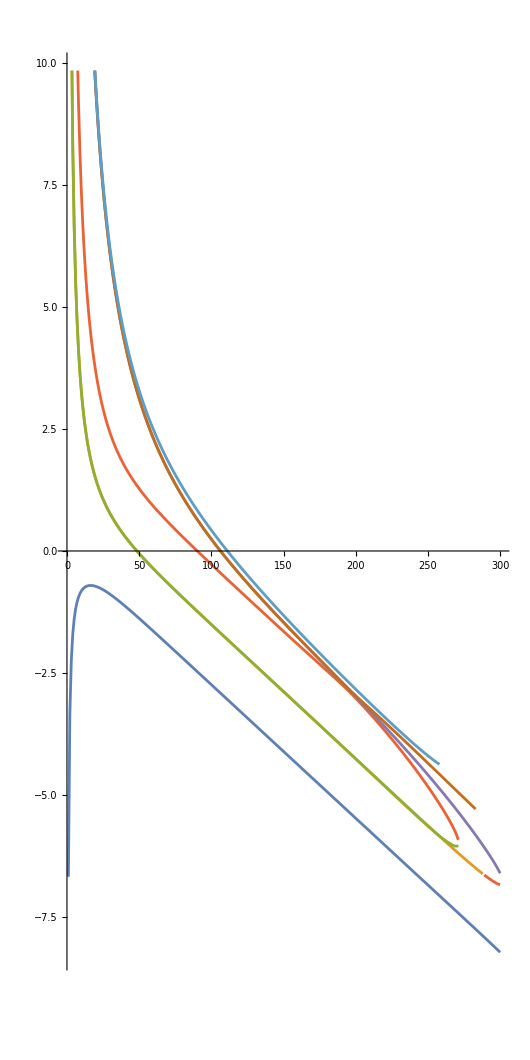

```mathematica
PlotL5=ListLinePlot[Transpose[EnergyTableL5],AspectRatio->2]
```

```mathematica
EnergyTableL5=Table[Sort[1/(i/100)Eigenvalues[H5[-(i/100)^(12/5)]]][[1;;7]]//Chop,{i,1,350}];
```

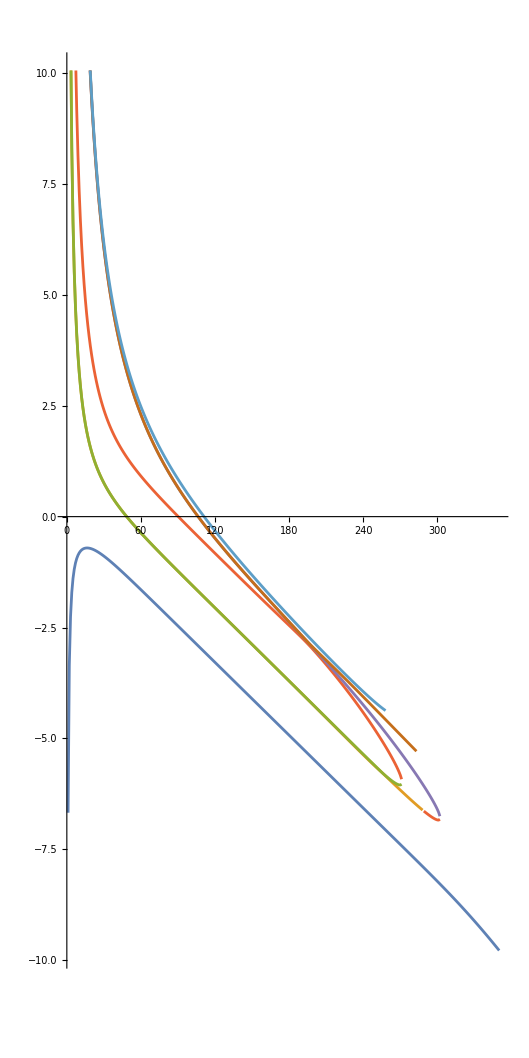

```mathematica
PlotL5=ListLinePlot[Transpose[EnergyTableL5],AspectRatio->2]
```

```mathematica
H[7,x]
```

{{-0.0666667+(2.+0. ⅈ) x κ,0.-(0.+1. ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-(0.+1. ⅈ) x,0.333333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+(0.036+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.333333+(1.+0. ⅈ) x κ,0.-(0.+1. ⅈ) x,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.036+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x},{0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.-(0.+1. ⅈ) x,0.733333,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,1.93333+(1.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.93333+(0.8+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.93333+(0.8+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.93333+(1.16+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.33333+(0.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0256+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,2.33333+(0.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0256+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.36+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.-(0.+0.4 ⅈ) x,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.32+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.36+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0360533+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0360533+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(1.+0. ⅈ) x κ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,4.73333,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.,0.,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.,4.73333,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.,0.,4.73333,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,4.73333,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(1.61466+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.93312+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.9936+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(1.568+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.93312+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.6224+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.544+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.9936+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.9936+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.544+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.6224+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.93312+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(1.568+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.9936+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.93312+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(1.61466+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.036+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0256+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0360533+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.614656+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.3136+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.784+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.3136+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.784+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.4+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.4+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.036+0. ⅈ) x κ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0256+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0360533+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.614656+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.784+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.3136+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.784+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.3136+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.4+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.4+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.73333,0.,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,6.73333,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,6.73333,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,6.73333}}

```mathematica
EnergyTableL7=Table[Sort[1/(i/100)Eigenvalues[H7[-(i/100)^(12/5)]]][[1;;7]]//Chop,{i,1,300}];
```

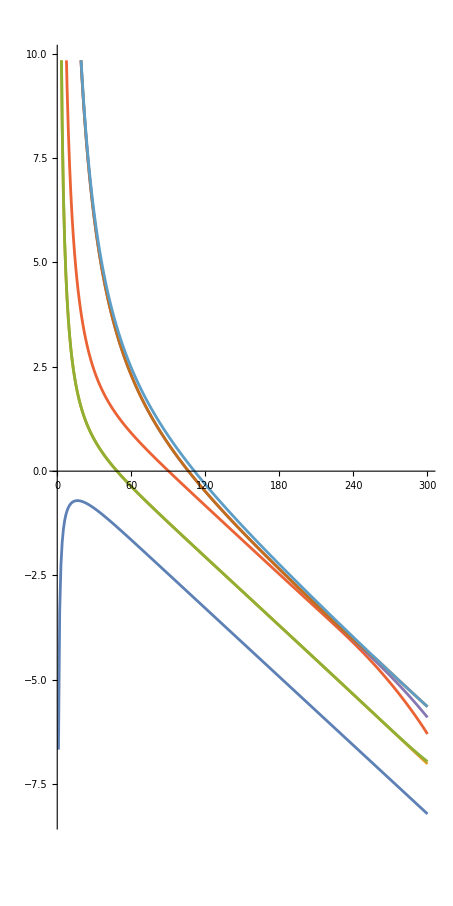

```mathematica
PlotL7=ListLinePlot[Transpose[EnergyTableL7],AspectRatio->2]
```

```mathematica
H[9,x]
```

```mathematica
EnergyTableL9=Table[Sort[1/(i/100)Eigenvalues[H9[-(i/100)^(12/5)]]][[1;;7]]//Chop,{i,1,350}];
```

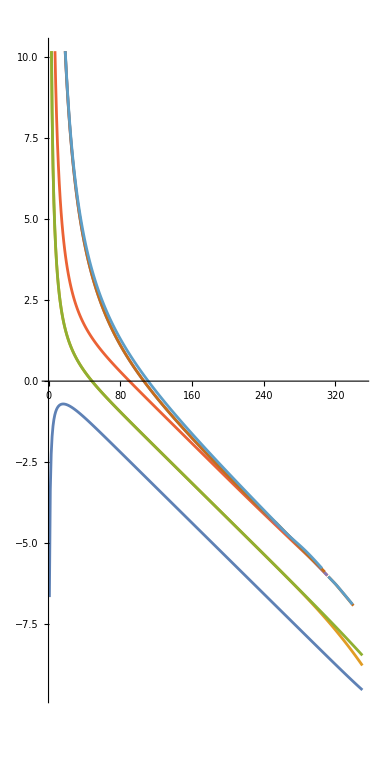

```mathematica
PlotL9=ListLinePlot[Transpose[EnergyTableL9],AspectRatio->2]
```

```mathematica
H[10,x]
```

{{-1/15+2 x κ,-ⅈ x,-ⅈ x,0,(x κ)/10,0,0,(x κ)/10,0,0,(4 x κ)/75,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,(ⅈ x)/55,0,0,0,(ⅈ x)/55,0,0,0,0,(9 x κ)/250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(9 x κ)/250,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,(441 x κ)/16250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 x κ)/16250,7/650 ⅈ √(3/95) x κ,0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,(x κ)/7410,0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,7/650 ⅈ √(3/95) x κ,0,(x κ)/7410,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(9 ⅈ x)/550,0,0,0,0,0,0,0,(9 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 x κ)/812500,(133 ⅈ x κ)/(32500 √3),0,0,0,0,0,0,0,0,0,0,0,(133 ⅈ x κ)/(32500 √3),0,0,0,0,0,0,0,0,0,0,0,(x κ)/3900,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(133 ⅈ x κ)/(32500 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(133 ⅈ x κ)/(32500 √3),0,0,0,0,0,0,0,(x κ)/3900},{-ⅈ x,1/3+x κ,0,-ⅈ x,0,0,0,-(2 ⅈ x)/5,(x κ)/10,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,(4 x κ)/75,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(8 ⅈ x)/125,(9 x κ)/250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(26 ⅈ x)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 x κ)/16250,7/650 ⅈ √(3/95) x κ,7/650 ⅈ √(3/95) x κ,(x κ)/7410,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(9 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(468 ⅈ x)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-ⅈ x,0,1/3+x κ,-ⅈ x,-(2 ⅈ x)/5,0,0,0,0,(x κ)/10,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,(ⅈ x)/55,-(8 ⅈ x)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(9 x κ)/250,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,-(26 ⅈ x)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 x κ)/16250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,(x κ)/7410,0,0,0,0,0,(9 ⅈ x)/550,0,0,0,-(468 ⅈ x)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-ⅈ x,-ⅈ x,11/15,0,0,0,0,-(2 ⅈ x)/5,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(8 ⅈ x)/125,0,0,0,0,0,0,0,0,-(8 ⅈ x)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(26 ⅈ x)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(26 ⅈ x)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(x κ)/10,0,-(2 ⅈ x)/5,0,29/15+(29 x κ)/25,0,0,0,-ⅈ x,0,(49 x κ)/750,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(9 x κ)/250,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,(147 x κ)/24700,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,0,(64 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11858 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 x κ)/16250,0,0,0,0,0,0,0,(616 ⅈ x κ)/(40625 √3),0,0,0,0,0,0,0,0,0,0,0,(616 ⅈ x κ)/(40625 √3),0,0,0,0,0,0,0,0,0,0,0,(32 x κ)/4875,0,0,0,0,0,0,0,0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,(x κ)/7410,0,0,0},{0,0,0,0,0,29/15+(4 x κ)/5,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(8 x)/275,0,0,0,0,0,0,0,0,0,0,0,-(8 x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1617 ⅈ x κ)/(40625 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1617 ⅈ x κ)/(40625 √5),0,0,0,0,0,0,0,-(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,-(28 √(3/5) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,(4 ⅈ x κ)/(975 √19),0,0,0,0,0,0,0,0,0,0,0,-(28 √(3/5) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,-(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,(4 ⅈ x κ)/(975 √19),0,0},{0,0,0,0,0,0,29/15+(4 x κ)/5,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(8 x)/275,0,0,0,0,0,0,0,0,0,0,0,-(8 x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1617 ⅈ x κ)/(40625 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1617 ⅈ x κ)/(40625 √5),0,0,0,-(28 √(3/5) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(77 x κ)/(8125 √57),0,0,0,0,0,0,0,(4 ⅈ x κ)/(975 √19),0,0,0,0,0,0,0,0,0,0,0,-(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(28 √(3/5) x κ)/1625,0,0,0,0,0,0,0,(4 ⅈ x κ)/(975 √19),0},{(x κ)/10,-(2 ⅈ x)/5,0,0,0,0,0,29/15+(29 x κ)/25,0,-ⅈ x,0,0,0,0,(x κ)/10,0,0,0,(49 x κ)/750,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,(9 x κ)/250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,(147 x κ)/24700,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(64 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 x κ)/16250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11858 x κ)/1015625,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,(x κ)/7410,0,0,0,0,0,0,0,0,0,0,0,(616 ⅈ x κ)/(40625 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(616 ⅈ x κ)/(40625 √3),0,0,0,0,0,0,0,(32 x κ)/4875},{0,(x κ)/10,0,-(2 ⅈ x)/5,-ⅈ x,0,0,0,7/3+(4 x κ)/25,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(8 ⅈ x)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2601 x κ)/162500,(357 ⅈ √(3/95) x κ)/6500,(357 ⅈ √(3/95) x κ)/6500,(147 x κ)/24700,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(64 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(26 ⅈ x)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(x κ)/10,-(2 ⅈ x)/5,0,0,0,-ⅈ x,0,7/3+(4 x κ)/25,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,-(8 ⅈ x)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,(147 x κ)/24700,0,0,0,0,0,(64 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,-(26 ⅈ x)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(4 x κ)/75,0,-(3 ⅈ x)/25,0,(49 x κ)/750,0,0,0,0,0,59/15+(914 x κ)/625,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,(338 x κ)/9375,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,(1568 x κ)/30875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(507 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(116427 x κ)/20312500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(9 x κ)/250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(4137 ⅈ √3 x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,-(4137 ⅈ √3 x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,(441 x κ)/32500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,59/15+(84 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ √3 x)/2750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10047 √(3/5) x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4137 ⅈ x κ)/(162500 √19),0,0,0,0,0,0,0,0,0,0,0,-(1071 ⅈ x κ)/(32500 √5),0,0,0,0,0,0,0,0,0,0,0,-(147 √(3/19) x κ)/6500,0,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,59/15+(34 x κ)/25,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(591 ⅈ √(3/130) x κ)/6250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(591 ⅈ √(3/130) x κ)/6250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(63 x κ)/(250 √130),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(63 x κ)/(250 √130),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,59/15+(84 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ √3 x)/2750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10047 √(3/5) x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,-(1071 ⅈ x κ)/(32500 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4137 ⅈ x κ)/(162500 √19),0,0,0,0,0,0,0,-(147 √(3/19) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(x κ)/10,0,0,(x κ)/10,-(2 ⅈ x)/5,-(2 ⅈ x)/5,0,0,0,0,59/15+(8 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,(147 x κ)/24700,0,0,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,(147 x κ)/24700,0,0,0},{0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,59/15+(84 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ √3 x)/2750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10047 √(3/5) x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(1071 ⅈ x κ)/(32500 √5),0,0,0,0,0,0,0,0,0,0,0,(4137 ⅈ x κ)/(162500 √19),0,0,0,0,0,0,0,0,0,0,0,-(147 √(3/19) x κ)/6500,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,59/15+(34 x κ)/25,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(591 ⅈ √(3/130) x κ)/6250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(591 ⅈ √(3/130) x κ)/6250,0,0,0,0,0,0,(63 x κ)/(250 √130),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(63 x κ)/(250 √130),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,59/15+(84 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ √3 x)/2750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10047 √(3/5) x κ)/812500,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4137 ⅈ x κ)/(162500 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(1071 ⅈ x κ)/(32500 √5),0,0,0,0,0,0,0,-(147 √(3/19) x κ)/6500,0},{(4 x κ)/75,-(3 ⅈ x)/25,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,59/15+(914 x κ)/625,0,0,0,(588 ⅈ x)/1375,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,(1568 x κ)/30875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(507 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(9 x κ)/250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(116427 x κ)/20312500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(4137 ⅈ √3 x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(4137 ⅈ √3 x κ)/812500,0,0,0,0,0,0,0,(441 x κ)/32500},{0,(4 x κ)/75,0,-(3 ⅈ x)/25,0,0,0,0,(49 x κ)/750,0,-ⅈ x,0,0,0,0,0,0,0,0,13/3+(289 x κ)/625,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,-(3136 ⅈ x κ)/(8125 √285),-(3136 ⅈ x κ)/(8125 √285),(1568 x κ)/30875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(507 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(8 ⅈ x)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,13/3+(17 x κ)/25,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(56 √(2/143) x)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8/25 ⅈ √(6/143) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,13/3+(17 x κ)/25,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(56 √(2/143) x)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8/25 ⅈ √(6/143) x,0,0,0,0,0,0,0,0,0,0},{(ⅈ x)/55,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,13/3+x κ,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,(21 √(57/5) x)/7150,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(784 ⅈ x)/11171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 √3 x)/89375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 √3 x)/89375,0,0,0,0,0,0,0,(48 ⅈ x)/715},{0,0,(4 x κ)/75,-(3 ⅈ x)/25,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,13/3+(289 x κ)/625,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,(1568 x κ)/30875,0,0,0,0,0,(507 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(8 ⅈ x)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,13/3+(17 x κ)/25,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(56 √(2/143) x)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8/25 ⅈ √(6/143) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,13/3+(17 x κ)/25,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,-(56 √(2/143) x)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8/25 ⅈ √(6/143) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(ⅈ x)/55,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,13/3+x κ,-ⅈ x,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,(784 ⅈ x)/11171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 √3 x)/89375,0,0,0,0,0,0,0,0,0,0,0,(112 √3 x)/89375,0,0,0,0,0,0,0,0,0,0,0,(48 ⅈ x)/715,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,(ⅈ x)/55,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,-ⅈ x,71/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/893750,(21 √(57/5) x)/7150,(21 √(57/5) x)/7150,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,71/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,71/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅈ x)/55,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,(588 ⅈ x)/1375,0,0,0,0,0,0,71/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,(21 √(57/5) x)/7150,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(9 x κ)/250,0,-(8 ⅈ x)/125,0,(16 x κ)/625,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,89/15+(25229 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,(23716 x κ)/463125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1296 ⅈ x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(187272 x κ)/25390625,0,0,0,0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(5712 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,-(5712 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/121875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(2916 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √3 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11424 √(3/5) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(17136 ⅈ x κ)/(203125 √19),0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(121875 √5),0,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,89/15+(621 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1224 √(2/65) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/625 ⅈ √(2/195) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(196 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(204 ⅈ √(6/65) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,(204 ⅈ √(6/65) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/375 √(2/65) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/375 √(2/65) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(2916 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √3 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11424 √(3/5) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(121875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(17136 ⅈ x κ)/(203125 √19),0,0,0,0,0,0,0,(1568 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,(4 x κ)/75,0,-(3 ⅈ x)/25,(x κ)/10,0,0,0,(49 x κ)/750,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(389 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,0,0,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,(1568 x κ)/30875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(68 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(621 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,(1224 √(2/65) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/625 ⅈ √(2/195) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(621 x κ)/625,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1224 √(2/65) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/625 ⅈ √(2/195) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(68 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(4 x κ)/75,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,(49 x κ)/750,0,0,0,(x κ)/10,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(389 x κ)/625,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/30875,0,0,0},{0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(2916 x κ)/3125,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √3 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,(11424 √(3/5) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(121875 √5),0,0,0,0,0,0,0,0,0,0,0,-(17136 ⅈ x κ)/(203125 √19),0,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/(8125 √57),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(196 x κ)/125,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(204 ⅈ √(6/65) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,(204 ⅈ √(6/65) x κ)/3125,0,0,0,0,0,0,0,0,0,56/375 √(2/65) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/375 √(2/65) x κ,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(621 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,(1224 √(2/65) x κ)/15625,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/625 ⅈ √(2/195) x κ,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(2916 x κ)/3125,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √3 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,(11424 √(3/5) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(17136 ⅈ x κ)/(203125 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(121875 √5),0,0,0,0,0,0,0,(1568 x κ)/(8125 √57),0},{(9 x κ)/250,-(8 ⅈ x)/125,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,89/15+(25229 x κ)/15625,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,(23716 x κ)/463125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1296 ⅈ x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,0,0,0,0,(187272 x κ)/25390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(5712 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(5712 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,(1568 x κ)/121875},{0,(9 x κ)/250,0,-(8 ⅈ x)/125,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(9604 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(32041 x κ)/1015625,(27566 ⅈ x κ)/(40625 √285),(27566 ⅈ x κ)/(40625 √285),(23716 x κ)/463125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1296 ⅈ x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(196 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(196 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,91/25 ⅈ √(2/11) x,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,179/625 ⅈ √(2/13) x κ,0,0,-154/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(21 √(33/65) x)/1250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 ⅈ x)/(10 √715),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,19/3+(196 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,19/3+(196 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,91/25 ⅈ √(2/11) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,179/625 ⅈ √(2/13) x κ,0,0,-154/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(21 √(33/65) x)/1250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 ⅈ x)/(10 √715),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,19/3+(4 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0},{0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,19/3+(4 x κ)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(25 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/(406250 √2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √(3/2) x)/35750,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/10) x)/3250,0,0,0,0,0,0,0,0,0,0,0,21/286 ⅈ √(19/10) x,0,0},{0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,19/3+(4 x κ)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(25 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/(406250 √2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/10) x)/3250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √(3/2) x)/35750,0,0,0,0,0,0,0,21/286 ⅈ √(19/10) x,0},{(ⅈ x)/55,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,19/3+4 x κ,0,0,0,0,0,0,0,0,0,0,0,0,-4 ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,-(161 √(57/5) x)/7150,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2 x κ)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4851 ⅈ x)/4062500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √3 x)/32500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √3 x)/32500,0,0,0,0,0,0,0,(147 ⅈ x)/2860},{0,0,(9 x κ)/250,-(8 ⅈ x)/125,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,19/3+(9604 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,(23716 x κ)/463125,0,0,0,0,0,(1296 ⅈ x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(196 x κ)/125,0,0,0,0,0,0,0,0,0,91/25 ⅈ √(2/11) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,179/625 ⅈ √(2/13) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(21 √(33/65) x)/1250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 ⅈ x)/(10 √715),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(196 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(196 x κ)/125,0,0,0,0,0,0,91/25 ⅈ √(2/11) x,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,179/625 ⅈ √(2/13) x κ,0,0,0,0,0,0,0,0,0,0,0,0,-154/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(21 √(33/65) x)/1250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 ⅈ x)/(10 √715),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(196 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(ⅈ x)/55,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+4 x κ,0,0,0,-4 ⅈ x,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2 x κ)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4851 ⅈ x)/4062500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √3 x)/32500,0,0,0,0,0,0,0,0,0,0,0,(147 √3 x)/32500,0,0,0,0,0,0,0,0,0,0,0,(147 ⅈ x)/2860,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(4 x κ)/5,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(25 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/(406250 √2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/10) x)/3250,0,0,0,0,0,0,0,0,0,0,0,(147 √(3/2) x)/35750,0,0,0,0,0,0,0,0,0,0,0,21/286 ⅈ √(19/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(4 x κ)/5,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(25 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/(406250 √2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √(3/2) x)/35750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/10) x)/3250,0,0,0,0,0,0,0,21/286 ⅈ √(19/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19/3+(4 x κ)/25,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,(ⅈ x)/55,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,-4 ⅈ x,0,0,0,101/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,-(161 √(57/5) x)/7150,-(161 √(57/5) x)/7150,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(8 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,91/25 ⅈ √(2/11) x,0,0,0,0,0,0,0,0,0,91/25 ⅈ √(2/11) x,0,0,0,0,0,0,101/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(322 x)/(125 √143),0,0,-2 ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(322 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,91/25 ⅈ √(2/11) x,0,0,0,0,0,91/25 ⅈ √(2/11) x,0,0,0,0,0,0,0,0,0,101/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(322 x)/(125 √143),0,0,-2 ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,-(322 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(ⅈ x)/55,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4 ⅈ x,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,101/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(8 ⅈ x)/5,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,-(161 √(57/5) x)/7150,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(441 x κ)/16250,0,-(26 ⅈ x)/625,0,(2601 x κ)/162500,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,0,0,0,119/15+(113722274 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6385729 ⅈ x)/8937500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(101183481 x κ)/3300781250,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1807267 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,(1807267 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,(581042 x κ)/7921875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,119/15+(1083136 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(13/2) x)/68750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1800561 x κ)/(5078125 √130),0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(6/247) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,(96481 ⅈ √(2/195) x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,(83006 √(2/247) x κ)/121875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(255544 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3353 √(3/5) x κ)/78125,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1078 ⅈ x κ)/(9375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,119/15+(45664 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(23471 √(3/5) x κ)/406250,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3773 ⅈ x κ)/(24375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(13814 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,119/15+(1083136 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(13/2) x)/68750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1800561 x κ)/(5078125 √130),0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(96481 ⅈ √(2/195) x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(6/247) x κ)/1015625,0,0,0,0,0,0,0,(83006 √(2/247) x κ)/121875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,(9 x κ)/250,0,-(8 ⅈ x)/125,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,119/15+(12104 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,(23716 x κ)/463125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(2516 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(392 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(45664 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,(23471 √(3/5) x κ)/406250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,(3773 ⅈ x κ)/(24375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(255544 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3353 √(3/5) x κ)/78125,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1078 ⅈ x κ)/(9375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(2516 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,(4 x κ)/75,-(3 ⅈ x)/25,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(578 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(2516 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(255544 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,(3353 √(3/5) x κ)/78125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1078 ⅈ x κ)/(9375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(45664 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(23471 √(3/5) x κ)/406250,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3773 ⅈ x κ)/(24375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(392 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(2516 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(9 x κ)/250,0,0,0,-(8 ⅈ x)/125,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,(x κ)/10,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(12104 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,(23716 x κ)/463125,0,0,0},{0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1083136 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(13/2) x)/68750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,(1800561 x κ)/(5078125 √130),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(96481 ⅈ √(2/195) x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(6/247) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,(83006 √(2/247) x κ)/121875,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(13814 x κ)/8125,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(45664 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,(23471 √(3/5) x κ)/406250,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3773 ⅈ x κ)/(24375 √5),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(255544 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,(3353 √(3/5) x κ)/78125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1078 ⅈ x κ)/(9375 √5),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1083136 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(13/2) x)/68750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,(1800561 x κ)/(5078125 √130),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(6/247) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(96481 ⅈ √(2/195) x κ)/203125,0,0,0,0,0,0,0,(83006 √(2/247) x κ)/121875,0},{(441 x κ)/16250,-(26 ⅈ x)/625,0,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,(441 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(113722274 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6385729 ⅈ x)/8937500,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,(101183481 x κ)/3300781250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1807267 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1807267 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,(581042 x κ)/7921875},{7/650 ⅈ √(3/95) x κ,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(659358 x κ)/528125,0,0,0,0,-(71148 x κ)/10034375,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 √(19/5) x κ)/5281250,0,0,(x κ)/10,0,0,0,0,0,0,0,0,-(83006 x κ)/(7921875 √95),0,0,0,0,0,0,0,0,0,0,0,-(539 ⅈ √(19/15) x κ)/105625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(5112 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/550 √(741/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13783 ⅈ √(2/741) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(19/26) x κ)/40625,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,-(11858 √(2/65) x κ)/2315625,0,0,0,0,0,0,0,-(77 ⅈ √(2/195) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1428 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ x κ)/(46875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/625 √(19/3) x κ,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1464 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(539 ⅈ x κ)/(121875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 √(19/3) x κ)/3250,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,119/15+(714 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0},{7/650 ⅈ √(3/95) x κ,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(71148 x κ)/10034375,0,0,0,0,119/15+(659358 x κ)/528125,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(83006 x κ)/(7921875 √95),0,0,0,0,0,0,0,0,0,0,0,(10059 √(19/5) x κ)/5281250,0,0,0,0,0,0,(x κ)/10,0,0,0,0,-(539 ⅈ √(19/15) x κ)/105625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(5112 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/550 √(741/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13783 ⅈ √(2/741) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(11858 √(2/65) x κ)/2315625,0,0,0,0,0,0,0,0,0,0,0,(179 √(19/26) x κ)/40625,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,-(77 ⅈ √(2/195) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1428 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ x κ)/(46875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/625 √(19/3) x κ,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1464 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(539 ⅈ x κ)/(121875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 √(19/3) x κ)/3250,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(714 x κ)/625,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(x κ)/7410,0,0,0,(147 x κ)/24700,0,0,0,0,0,(1568 x κ)/30875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,(23716 x κ)/463125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,119/15+(4586 x κ)/4225,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/2860,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11858 x κ)/752578125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(77 ⅈ x κ)/(528125 √3),0,0,0,0,0,0,0,0,0,0,0,-(77 ⅈ x κ)/(528125 √3),0,0,0,0,0,0,0,0,0,0,0,(19 x κ)/42250,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(714 x κ)/625,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,-1/650 ⅈ √19 x κ,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1464 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(539 ⅈ x κ)/(121875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,(7 √(19/3) x κ)/3250,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1428 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ x κ)/(46875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,1/625 √(19/3) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(5112 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/550 √(741/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13783 ⅈ √(2/741) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,(179 √(19/26) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,-(11858 √(2/65) x κ)/2315625,0,0,0,0,0,0,0,0,0,0,0,-(77 ⅈ √(2/195) x κ)/1625,0,0},{7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(659358 x κ)/528125,0,0,0,0,0,-(71148 x κ)/10034375,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,(10059 √(19/5) x κ)/5281250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(83006 x κ)/(7921875 √95),0,0,0,0,0,0,0,-(539 ⅈ √(19/15) x κ)/105625},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,119/15+(38 x κ)/65,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,-1/650 ⅈ √19 x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(714 x κ)/625,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1464 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(539 ⅈ x κ)/(121875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,(7 √(19/3) x κ)/3250,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(1428 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ x κ)/(46875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,1/625 √(19/3) x κ,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,119/15+(5112 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/550 √(741/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13783 ⅈ √(2/741) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(11858 √(2/65) x κ)/2315625,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,(179 √(19/26) x κ)/40625,0,0,0,0,0,0,0,-(77 ⅈ √(2/195) x κ)/1625,0},{7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(71148 x κ)/10034375,0,0,0,0,0,119/15+(659358 x κ)/528125,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(83006 x κ)/(7921875 √95),0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,(10059 √(19/5) x κ)/5281250,0,0,0,0,0,0,0,-(539 ⅈ √(19/15) x κ)/105625},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,119/15+(38 x κ)/65,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,-1/650 ⅈ √19 x κ,0,0,0,0},{(x κ)/7410,0,0,0,0,0,0,(147 x κ)/24700,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/30875,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(23716 x κ)/463125,0,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,119/15+(4586 x κ)/4225,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/2860,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11858 x κ)/752578125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(77 ⅈ x κ)/(528125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(77 ⅈ x κ)/(528125 √3),0,0,0,0,(x κ)/10,0,0,(19 x κ)/42250},{0,(441 x κ)/16250,0,-(26 ⅈ x)/625,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(47706649 x κ)/66015625,(1063678 ⅈ √(3/95) x κ)/2640625,(1063678 ⅈ √(3/95) x κ)/2640625,(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6385729 ⅈ x)/8937500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,25/3+(131233 x κ)/528125,-(71148 x κ)/10034375,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,-(71148 x κ)/10034375,25/3+(131233 x κ)/528125,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,(x κ)/7410,0,0,0,0,0,0,(147 x κ)/24700,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/30875,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(23716 x κ)/463125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,(71148 x κ)/10034375,-(154 ⅈ √(57/5) x κ)/21125,-(154 ⅈ √(57/5) x κ)/21125,25/3+(361 x κ)/4225,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/2860,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(117419 x κ)/203125,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,179/625 ⅈ √(2/13) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(322 x)/(125 √143),0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(27628 x κ)/40625,0,0,(616 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(124326 x κ)/40625,0,0,-(2772 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(22743 ⅈ x)/(625 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,25/3+(323 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(616 ⅈ √(3/95) x κ)/1625,0,0,25/3+(76 x κ)/325,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2772 ⅈ √(3/95) x κ)/1625,0,0,25/3+(342 x κ)/325,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9/5 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(117419 x κ)/203125,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,179/625 ⅈ √(2/13) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(322 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(27628 x κ)/40625,0,0,(616 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(124326 x κ)/40625,0,0,-(2772 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(22743 ⅈ x)/(625 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,25/3+(323 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(616 ⅈ √(3/95) x κ)/1625,0,0,25/3+(76 x κ)/325,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2772 ⅈ √(3/95) x κ)/1625,0,0,25/3+(342 x κ)/325,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9/5 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(289 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(25 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(68 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(306 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,252/25 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1176 ⅈ √13 x)/171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 √39 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(25 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(68 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,(2 x κ)/5,0,0,0,0,0,0,0,0,0,0,0,0,-(8 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(16 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0},{0,0,0,0,0,-(8 x)/275,0,0,0,0,0,0,0,0,0,(91 ⅈ √3 x)/2750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √3 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(13/2) x)/68750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/550 √(741/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(72 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13524 ⅈ x)/(171875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(3/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,-(84 √57 x)/6875,0,0,0,0,0,0,0,0,0,0,0,3/55 ⅈ √19 x,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(306 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,252/25 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1176 ⅈ √13 x)/171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 √39 x)/1375,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-(8 x)/275,0,0,0,0,0,0,0,0,0,0,(91 ⅈ √3 x)/2750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √3 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(13/2) x)/68750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/550 √(741/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(72 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13524 ⅈ x)/(171875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(84 √57 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(3/5) x)/1375,0,0,0,0,0,0,0,3/55 ⅈ √19 x,0},{(9 ⅈ x)/550,0,0,0,0,0,0,(64 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,(507 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1296 ⅈ x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6385729 ⅈ x)/8937500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,(57 ⅈ x)/2860,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(324 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(324 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(183456 ⅈ x)/4296875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2184 √3 x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2184 √3 x)/34375,0,0,0,0,0,0,0,(78 ⅈ x)/275},{0,0,(441 x κ)/16250,-(26 ⅈ x)/625,0,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(47706649 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,(71148 x κ)/10034375,0,0,0,0,0,(6385729 ⅈ x)/8937500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(124326 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2772 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,(22743 ⅈ x)/(625 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,179/625 ⅈ √(2/13) x κ,0,0,0,0,0,0,0,0,0,-(322 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(27628 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(616 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(117419 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(124326 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,-(2772 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,(22743 ⅈ x)/(625 √143),0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,179/625 ⅈ √(2/13) x κ,0,0,0,0,0,0,-(322 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(27628 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,(616 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(117419 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(9 ⅈ x)/550,0,0,0,(64 ⅈ x)/1375,0,0,0,0,0,(507 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1296 ⅈ x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6385729 ⅈ x)/8937500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,(57 ⅈ x)/2860,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(324 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(324 ⅈ x)/25,0,0,0,0,0,0,0,0,(183456 ⅈ x)/4296875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2184 √3 x)/34375,0,0,0,0,0,0,0,0,0,0,0,-(2184 √3 x)/34375,0,0,0,0,0,0,0,0,0,0,0,(78 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-(8 x)/275,0,0,0,0,0,(91 ⅈ √3 x)/2750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √3 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(13/2) x)/68750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/550 √(741/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(72 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13524 ⅈ x)/(171875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(84 √57 x)/6875,0,0,0,0,0,0,0,0,0,0,0,-(161 √(3/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,3/55 ⅈ √19 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(306 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,252/25 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,(1176 ⅈ √13 x)/171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 √39 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-(8 x)/275,0,0,0,0,0,0,(91 ⅈ √3 x)/2750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √3 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(13/2) x)/68750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/550 √(741/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(72 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13524 ⅈ x)/(171875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(3/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(84 √57 x)/6875,0,0,0,0,0,0,0,3/55 ⅈ √19 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,(49 ⅈ x)/550,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(108 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2 x κ)/5,0,0,0,-(8 ⅈ x)/5,0,0,0,0,0,0,0,0,0,(8281 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(16 x κ)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(25 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(68 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(306 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,252/25 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1176 ⅈ √13 x)/171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 √39 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(7 x)/(55 √10),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36/275 ⅈ √(6/5) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(25 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(637 ⅈ √(6/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(68 x κ)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,(4 x κ)/75,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(289 x κ)/625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(131233 x κ)/528125,0,0,0,-(71148 x κ)/10034375,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2772 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(342 x κ)/325,0,0,0,0,0,0,0,0,9/5 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/25 √(2/3705) x κ,0,0,0,0,0,0,-2 ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(616 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(76 x κ)/325,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(323 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(71148 x κ)/10034375,0,0,0,25/3+(131233 x κ)/528125,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2527 ⅈ x)/(250 √143),0,0,0,0,1/2 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2772 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(342 x κ)/325,0,0,0,0,0,0,9/5 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,-2 ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 ⅈ x)/(25 √22),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(616 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(76 x κ)/325,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14/5 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3+(323 x κ)/1625,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(x κ)/7410,0,0,0,0,0,0,(147 x κ)/24700,0,0,0,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/30875,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(23716 x κ)/463125,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,25/3+(361 x κ)/4225,0,0,0,0,0,(57 ⅈ x)/2860,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0},{0,(9 ⅈ x)/550,0,0,0,0,0,0,(64 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,(507 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1296 ⅈ x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6385729 ⅈ x)/8937500,-(2527 √(57/5) x)/71500,-(2527 √(57/5) x)/71500,(57 ⅈ x)/2860,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(324 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,131/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(22743 ⅈ x)/(625 √143),0,0,9/5 √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(22743 ⅈ x)/(625 √143),0,0,0,0,0,0,0,0,0,0,0,0,9/5 √(57/715) x,0,0,0,0,0,0,0,0,131/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,252/25 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,131/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(22743 ⅈ x)/(625 √143),0,0,9/5 √(57/715) x,0,0,0,0,0,0,0,0,0,0,(22743 ⅈ x)/(625 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9/5 √(57/715) x,0,0,0,0,0,0,131/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,252/25 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,131/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(9 ⅈ x)/550,0,0,0,0,0,0,(64 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,(507 ⅈ x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1296 ⅈ x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(324 ⅈ x)/25,(6385729 ⅈ x)/8937500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,-(2527 √(57/5) x)/71500,0,0,0,(57 ⅈ x)/2860,0,0,0,0,0,131/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,252/25 ⅈ √(3/55) x,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,131/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13/275 √(3/10) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(216 ⅈ √(2/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,252/25 ⅈ √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,(17689 ⅈ √(3/65) x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,-21/275 √(19/13) x,0,0,0,0,0,0,0,0,0,0,0,0,131/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ x)/55,0,0,0,(ⅈ x)/55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,(72 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(588 ⅈ x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,131/15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(17689 x κ)/812500,0,-(468 ⅈ x)/15625,0,(11858 x κ)/1015625,0,0,0,0,0,(116427 x κ)/20312500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(784 ⅈ x)/11171875,0,0,0,0,(187272 x κ)/25390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4851 ⅈ x)/4062500,0,0,0,0,0,0,0,(101183481 x κ)/3300781250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(3/95) x κ)/66015625,0,0,0,0,(258181 ⅈ √(3/95) x κ)/66015625,0,0,0,0,(11858 x κ)/752578125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(183456 ⅈ x)/4296875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(74651480381 x κ)/41259765625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112564144 ⅈ √3 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,(112564144 ⅈ √3 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,(1138368 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(1617 ⅈ x κ)/(40625 √5),0,0,0,0,0,(10047 √(3/5) x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11424 √(3/5) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/(406250 √2),0,0,0,0,0,0,0,(1800561 x κ)/(5078125 √130),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13783 ⅈ √(2/741) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13524 ⅈ x)/(171875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1922299988 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(28141036 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,(4254712 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(591 ⅈ √(3/130) x κ)/6250,0,0,0,0,0,0,0,0,0,0,0,0,-(56 √(2/143) x)/3125,0,0,0,0,0,0,0,(1224 √(2/65) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3353 √(3/5) x κ)/78125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ x κ)/(46875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1176 ⅈ √13 x)/171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(35173557 x κ)/25390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(60368 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(204 ⅈ √(6/65) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(21 √(33/65) x)/1250,0,0,0,0,0,0,0,0,0,0,0,0,(23471 √(3/5) x κ)/406250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(539 ⅈ x κ)/(121875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(7087728 x κ)/5078125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10472 ⅈ √3 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1228843 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(365468 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(1617 ⅈ x κ)/(40625 √5),0,0,0,0,0,0,(10047 √(3/5) x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11424 √(3/5) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/(406250 √2),0,0,0,0,0,0,0,0,0,0,(1800561 x κ)/(5078125 √130),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13783 ⅈ √(2/741) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13524 ⅈ x)/(171875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1922299988 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4254712 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(28141036 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,(441 x κ)/16250,0,-(26 ⅈ x)/625,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,(x κ)/10,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(58269149 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(953136 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(181119 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(27628 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1228843 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(591 ⅈ √(3/130) x κ)/6250,0,0,0,0,0,0,0,-(56 √(2/143) x)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1224 √(2/65) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3353 √(3/5) x κ)/78125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ x κ)/(46875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1176 ⅈ √13 x)/171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(35173557 x κ)/25390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(60368 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(953136 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(9 x κ)/250,0,0,0,0,-(8 ⅈ x)/125,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(16829 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(3332 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(181119 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(204 ⅈ √(6/65) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(21 √(33/65) x)/1250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(23471 √(3/5) x κ)/406250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(539 ⅈ x κ)/(121875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(7087728 x κ)/5078125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10472 ⅈ √3 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(204 ⅈ √(6/65) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,-(21 √(33/65) x)/1250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(23471 √(3/5) x κ)/406250,0,0,0,0,0,0,0,0,0,0,0,0,(539 ⅈ x κ)/(121875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(7087728 x κ)/5078125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10472 ⅈ √3 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(181119 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,(8 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,(91 x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(3332 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,(9 x κ)/250,0,0,0,0,0,0,0,0,-(8 ⅈ x)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(16 x κ)/625,0,0,0,0,0,0,0,0,0,(4 x κ)/75,0,0,0,0,0,0,0,0,0,-(3 ⅈ x)/25,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(338 x κ)/9375,0,0,0,0,0,(49 x κ)/750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(98 ⅈ x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(16829 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(953136 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(591 ⅈ √(3/130) x κ)/6250,0,0,0,0,0,0,0,-(56 √(2/143) x)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1224 √(2/65) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3353 √(3/5) x κ)/78125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ x κ)/(46875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1176 ⅈ √13 x)/171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(35173557 x κ)/25390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(60368 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1228843 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(27628 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 ⅈ √(2/13) x κ)/1875,0,0,0,0,0,0,0,0,0,0,-21/125 √(3/1430) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1253 x κ)/(3125 √78),0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(181119 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,(153 ⅈ x κ)/(1250 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(224 √(2/39) x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(26/3) x κ)/15625,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1127 ⅈ x)/(6875 √65),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(953136 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(441 x κ)/16250,0,0,0,-(26 ⅈ x)/625,0,0,0,0,0,(2601 x κ)/162500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(6272 x κ)/609375,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/893750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(32041 x κ)/1015625,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(25921 ⅈ x)/893750,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(58269149 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,(71148 x κ)/10034375,0,0,0},{0,0,0,0,0,(1617 ⅈ x κ)/(40625 √5),0,0,0,0,0,0,0,0,0,(10047 √(3/5) x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11424 √(3/5) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,(441 ⅈ x)/(406250 √2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1800561 x κ)/(5078125 √130),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13783 ⅈ √(2/741) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13524 ⅈ x)/(171875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1922299988 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4254712 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,(28141036 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,(284592 x κ)/(2640625 √95),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(365468 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1228843 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(204 ⅈ √(6/65) x κ)/3125,0,0,0,0,0,0,0,-(21 √(33/65) x)/1250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(23471 √(3/5) x κ)/406250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(539 ⅈ x κ)/(121875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(7087728 x κ)/5078125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10472 ⅈ √3 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(591 ⅈ √(3/130) x κ)/6250,0,0,0,0,-(56 √(2/143) x)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1224 √(2/65) x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3353 √(3/5) x κ)/78125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ x κ)/(46875 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1176 ⅈ √13 x)/171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(35173557 x κ)/25390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(60368 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(1617 ⅈ x κ)/(40625 √5),0,0,0,0,0,0,0,0,0,0,(10047 √(3/5) x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(11424 √(3/5) x κ)/1015625,0,0,0,0,0,0,0,0,(441 ⅈ x)/(406250 √2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1800561 x κ)/(5078125 √130),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13783 ⅈ √(2/741) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13524 ⅈ x)/(171875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1922299988 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(28141036 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4254712 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,(284592 x κ)/(2640625 √95),0},{(17689 x κ)/812500,-(468 ⅈ x)/15625,0,0,0,0,0,(11858 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,(116427 x κ)/20312500,0,0,0,(784 ⅈ x)/11171875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(187272 x κ)/25390625,0,0,0,0,0,0,0,0,(4851 ⅈ x)/4062500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(101183481 x κ)/3300781250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,(258181 ⅈ √(3/95) x κ)/66015625,0,(11858 x κ)/752578125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(183456 ⅈ x)/4296875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(74651480381 x κ)/41259765625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112564144 ⅈ √3 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112564144 ⅈ √3 x κ)/1650390625,0,0,0,0,0,0,0,(1138368 x κ)/66015625},{(133 ⅈ x κ)/(32500 √3),0,0,0,(616 ⅈ x κ)/(40625 √3),0,0,0,0,0,-(4137 ⅈ √3 x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 √3 x)/89375,0,0,0,0,-(5712 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √3 x)/32500,0,0,0,0,0,0,0,(1807267 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 √(19/5) x κ)/5281250,0,0,0,0,-(83006 x κ)/(7921875 √95),0,0,0,0,-(77 ⅈ x κ)/(528125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2184 √3 x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112564144 ⅈ √3 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(83923557 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,-(1138368 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,-(60368 ⅈ √3 x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-(77 x κ)/(8125 √57),0,0,0,0,0,(4137 ⅈ x κ)/(162500 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(17136 ⅈ x κ)/(203125 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/10) x)/3250,0,0,0,0,0,0,0,(258181 ⅈ √(6/247) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(11858 √(2/65) x κ)/2315625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(84 √57 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(28141036 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(8753196 x κ)/13203125,0,0,0,0,0,0,0,0,0,0,0,-(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,-(11704 ⅈ √3 x κ)/528125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-(28 √(3/5) x κ)/1625,0,0,0,0,0,0,-(1071 ⅈ x κ)/(32500 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(121875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √(3/2) x)/35750,0,0,0,0,0,0,0,0,0,0,(96481 ⅈ √(2/195) x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(19/26) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(3/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4254712 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1733136 x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,-(15092 ⅈ √(3/95) x κ)/105625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(215733 x κ)/528125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(71148 x κ)/10034375,0,0,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(63 x κ)/(250 √130),0,0,0,0,0,0,0,8/25 ⅈ √(6/143) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/625 ⅈ √(2/195) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1078 ⅈ x κ)/(9375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/625 √(19/3) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 √39 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(60368 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(37229 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(4072 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/375 √(2/65) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 ⅈ x)/(10 √715),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3773 ⅈ x κ)/(24375 √5),0,0,0,0,0,0,0,0,0,0,0,0,(7 √(19/3) x κ)/3250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10472 ⅈ √3 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(8036 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(4163 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(7887 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1428 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(18768 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(662343 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0},{(133 ⅈ x κ)/(32500 √3),0,0,0,(616 ⅈ x κ)/(40625 √3),0,0,0,0,0,-(4137 ⅈ √3 x κ)/812500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112 √3 x)/89375,0,0,0,0,-(5712 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √3 x)/32500,0,0,0,0,0,0,0,(1807267 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(83006 x κ)/(7921875 √95),0,0,0,0,(10059 √(19/5) x κ)/5281250,0,0,0,0,-(77 ⅈ x κ)/(528125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2184 √3 x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112564144 ⅈ √3 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(1138368 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,149/15+(83923557 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,-(60368 ⅈ √3 x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-(28 √(3/5) x κ)/1625,0,0,0,0,0,-(1071 ⅈ x κ)/(32500 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(121875 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 √(3/2) x)/35750,0,0,0,0,0,0,0,(96481 ⅈ √(2/195) x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(19/26) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(3/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4254712 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,149/15+(1733136 x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,-(15092 ⅈ √(3/95) x κ)/105625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(63 x κ)/(250 √130),0,0,0,0,0,0,0,0,0,0,0,0,8/25 ⅈ √(6/143) x,0,0,0,0,0,0,0,-112/625 ⅈ √(2/195) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1078 ⅈ x κ)/(9375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/625 √(19/3) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 √39 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(60368 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(37229 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/375 √(2/65) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 ⅈ x)/(10 √715),0,0,0,0,0,0,0,0,0,0,0,0,(3773 ⅈ x κ)/(24375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 √(19/3) x κ)/3250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10472 ⅈ √3 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(8036 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(7887 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(18768 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-(77 x κ)/(8125 √57),0,0,0,0,0,0,(4137 ⅈ x κ)/(162500 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(17136 ⅈ x κ)/(203125 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/10) x)/3250,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(6/247) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(11858 √(2/65) x κ)/2315625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(84 √57 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(28141036 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(8753196 x κ)/13203125,0,0,0,0,0,0,0,-(11704 ⅈ √3 x κ)/528125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(215733 x κ)/528125,0,0,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(4072 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(4163 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1428 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(662343 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(x κ)/3900,0,0,0,(32 x κ)/4875,0,0,0,0,0,(441 x κ)/32500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(48 ⅈ x)/715,0,0,0,0,(1568 x κ)/121875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(147 ⅈ x)/2860,0,0,0,0,0,0,0,(581042 x κ)/7921875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 ⅈ √(19/15) x κ)/105625,0,0,0,0,-(539 ⅈ √(19/15) x κ)/105625,0,0,0,0,(19 x κ)/42250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(78 ⅈ x)/275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1138368 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(60368 ⅈ √3 x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,-(60368 ⅈ √3 x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,149/15+(115229 x κ)/105625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(4 ⅈ x κ)/(975 √19),0,0,0,0,0,-(147 √(3/19) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,21/286 ⅈ √(19/10) x,0,0,0,0,0,0,0,(83006 √(2/247) x κ)/121875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(77 ⅈ √(2/195) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/55 ⅈ √19 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(11704 ⅈ √3 x κ)/528125,0,0,0,0,0,0,0,0,0,0,0,-(15092 ⅈ √(3/95) x κ)/105625,0,0,0,0,0,0,0,0,0,0,0,149/15+(10312 x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(4 ⅈ x κ)/(975 √19),0,0,0,0,0,0,-(147 √(3/19) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,21/286 ⅈ √(19/10) x,0,0,0,0,0,0,0,0,0,0,(83006 √(2/247) x κ)/121875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(77 ⅈ √(2/195) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/55 ⅈ √19 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(15092 ⅈ √(3/95) x κ)/105625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(11704 ⅈ √3 x κ)/528125,0,0,0,0,0,0,0,149/15+(10312 x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,(x κ)/7410,0,0,0,0,0,0,(147 x κ)/24700,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1568 x κ)/30875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,(23716 x κ)/463125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(57 ⅈ x)/286,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0,0,0,0,0,149/15+(1037 x κ)/4225,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(662343 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(18768 x κ)/15625,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1428 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(7887 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(4163 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/375 √(2/65) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(21 ⅈ x)/(10 √715),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3773 ⅈ x κ)/(24375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 √(19/3) x κ)/3250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10472 ⅈ √3 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(8036 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(4072 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(63 x κ)/(250 √130),0,0,0,0,0,0,0,8/25 ⅈ √(6/143) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/625 ⅈ √(2/195) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1078 ⅈ x κ)/(9375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/625 √(19/3) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 √39 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(60368 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(37229 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(215733 x κ)/528125,0,0,0,0,0,0,0,0,0,0,0,-(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0},{0,0,0,0,0,-(28 √(3/5) x κ)/1625,0,0,0,0,0,0,0,0,0,-(1071 ⅈ x κ)/(32500 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(121875 √5),0,0,0,0,0,0,0,0,0,0,(147 √(3/2) x)/35750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(96481 ⅈ √(2/195) x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(19/26) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(3/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4254712 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1733136 x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,-(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,-(15092 ⅈ √(3/95) x κ)/105625,0,0},{0,0,0,0,0,0,-(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,(4137 ⅈ x κ)/(162500 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(17136 ⅈ x κ)/(203125 √19),0,0,0,0,0,0,0,0,(21 √(57/10) x)/3250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(6/247) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(11858 √(2/65) x κ)/2315625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(84 √57 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(28141036 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(8753196 x κ)/13203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,-(11704 ⅈ √3 x κ)/528125,0},{(133 ⅈ x κ)/(32500 √3),0,0,0,0,0,0,(616 ⅈ x κ)/(40625 √3),0,0,0,0,0,0,0,0,0,0,-(4137 ⅈ √3 x κ)/812500,0,0,0,(112 √3 x)/89375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(5712 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,(147 √3 x)/32500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1807267 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 √(19/5) x κ)/5281250,0,0,0,0,0,-(83006 x κ)/(7921875 √95),0,-(77 ⅈ x κ)/(528125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2184 √3 x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112564144 ⅈ √3 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(83923557 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(1138368 x κ)/66015625,0,0,0,0,0,0,0,-(60368 ⅈ √3 x κ)/2640625},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,-1/650 ⅈ √19 x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,149/15+(671 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,149/15+(196 x κ)/325,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,149/15+(76 x κ)/325,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,149/15+(671 x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10059 ⅈ x κ)/(81250 √5),0,0,0,0,(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-168/625 √(13/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(662343 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 ⅈ x κ)/(625 √26),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ √(57/715) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 x)/(125 √143),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1428 x κ)/3125,0,0,0,0,0,0,0,0,0,0,0,(308 ⅈ √(3/95) x κ)/1625,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/25 √(2/3705) x κ,0,0,0,0,0,0,0,0,0,0,3/5 ⅈ √(19/286) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,539/375 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(13 ⅈ x κ)/(125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 x)/(25 √55),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(2618 ⅈ √(3/95) x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(4163 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-21/50 √(3/2470) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/125 ⅈ √(2/1235) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(154 ⅈ √(26/95) x κ)/1875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 ⅈ x κ)/(50 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7/275 √(57/13) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15092 ⅈ √(3/95) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(4072 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,7/650 ⅈ √(3/95) x κ,0,0,0,0,0,0,0,0,0,(357 ⅈ √(3/95) x κ)/6500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(8125 √285),0,0,0,0,0,0,0,0,0,0,(21 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(27566 ⅈ x κ)/(40625 √285),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(x κ)/10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(57/5) x)/7150,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 ⅈ x)/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1063678 ⅈ √(3/95) x κ)/2640625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(71148 x κ)/10034375,0,0,0,0,0,0,0,0,0,0,0,149/15+(215733 x κ)/528125,0,0,0,0,0,0,0,0,0,0,0,-(154 ⅈ √(57/5) x κ)/21125,0,0,0},{0,0,0,0,0,-(77 x κ)/(8125 √57),0,0,0,0,0,0,0,0,0,(4137 ⅈ x κ)/(162500 √19),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(17136 ⅈ x κ)/(203125 √19),0,0,0,0,0,0,0,0,0,0,(21 √(57/10) x)/3250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(258181 ⅈ √(6/247) x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(11858 √(2/65) x κ)/2315625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(84 √57 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(28141036 ⅈ √(3/95) x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,149/15+(8753196 x κ)/13203125,0,0,0,0,0,0,0,0,0,0,0,-(11704 ⅈ √3 x κ)/528125,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(18768 x κ)/15625,0,0,0,0,0,0,0,-(616 ⅈ √3 x κ)/8125,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(539 x κ)/(1625 √15),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/650 ⅈ √19 x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/5 ⅈ √(39/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1232 ⅈ √3 x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(7887 x κ)/8125,0,0,0,0,0,0,0,-154/325 ⅈ √(3/95) x κ,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,56/375 √(2/65) x κ,0,0,0,0,0,0,0,(21 ⅈ x)/(10 √715),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3773 ⅈ x κ)/(24375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(7 √(19/3) x κ)/3250,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(10472 ⅈ √3 x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(8036 x κ)/8125,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(63 x κ)/(250 √130),0,0,0,0,8/25 ⅈ √(6/143) x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-112/625 ⅈ √(2/195) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1078 ⅈ x κ)/(9375 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/625 √(19/3) x κ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(14 √39 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(60368 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(37229 x κ)/40625,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-(28 √(3/5) x κ)/1625,0,0,0,0,0,0,0,0,0,0,-(1071 ⅈ x κ)/(32500 √5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3136 ⅈ x κ)/(121875 √5),0,0,0,0,0,0,0,0,(147 √(3/2) x)/35750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(96481 ⅈ √(2/195) x κ)/203125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(179 √(19/26) x κ)/40625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(161 √(3/5) x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4254712 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(284592 x κ)/(2640625 √95),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(1733136 x κ)/2640625,0,0,0,0,0,0,0,-(15092 ⅈ √(3/95) x κ)/105625,0},{(133 ⅈ x κ)/(32500 √3),0,0,0,0,0,0,(616 ⅈ x κ)/(40625 √3),0,0,0,0,0,0,0,0,0,0,-(4137 ⅈ √3 x κ)/812500,0,0,0,(112 √3 x)/89375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(5712 ⅈ √3 x κ)/1015625,0,0,0,0,0,0,0,0,(147 √3 x)/32500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1807267 ⅈ √3 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(83006 x κ)/(7921875 √95),0,0,0,0,0,(10059 √(19/5) x κ)/5281250,0,-(77 ⅈ x κ)/(528125 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2184 √3 x)/34375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(112564144 ⅈ √3 x κ)/1650390625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(1138368 x κ)/66015625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,149/15+(83923557 x κ)/66015625,0,0,0,0,0,0,0,-(60368 ⅈ √3 x κ)/2640625},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0

```mathematica
EnergyTableL10=Table[Sort[1/(i/100)Eigenvalues[H10[-(i/100)^(12/5)]]][[1;;12]]//Chop,{i,1,200}];
```

```mathematica
H[11,x]
```

{{-0.0666667+(2.+0. ⅈ) x κ,0.-(0.+1. ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0271385 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0271385 ⅈ) κ),0.-ⅈ x ((0.+0. ⅈ)-(0.00191374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00191374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.000134953 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00191374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00191374+0. ⅈ) κ),0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.000134953 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0163636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0163636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0217711 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0217711 ⅈ) κ),0.-ⅈ x ((0.+0. ⅈ)-(0.00236269+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00236269+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00025641 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00236269+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00236269+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00025641 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0145455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0145455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-(0.+1. ⅈ) x,0.333333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+(0.036+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0416 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0271385+0. ⅈ) x κ,0.+(0.+0.00191374 ⅈ) x κ,0.+(0.+0.00191374 ⅈ) x κ,0.+(0.000134953+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0163636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.029952 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0217711+0. ⅈ) x κ,0.+(0.+0.00236269 ⅈ) x κ,0.+(0.+0.00236269 ⅈ) x κ,0.+(0.00025641+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0145455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.333333+(1.+0. ⅈ) x κ,0.-(0.+1. ⅈ) x,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.036+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.-(0.+0.0416 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0271385+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00191374 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00191374 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.000134953+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0163636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.029952 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0217711+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00236269 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00236269 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00025641+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0145455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.-(0.+1. ⅈ) x,0.733333,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0416 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0416 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.029952 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.029952 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,1.93333+(1.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0160062 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00976009+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00976009+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00595142 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0465455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0116756 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0271385 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00875441+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00875441+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0065641 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00191374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00191374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.000134953 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0163636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0294545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.93333+(0.8+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0240046+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0240046+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0146373 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0146373 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0290909+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0290909+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0178005+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0178005+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.00125525 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0133469 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.000941193+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0133469 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.00125525 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.000941193+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0219541+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0219541+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.93333+(0.8+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0240046+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0240046+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0146373 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0146373 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0290909+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0290909+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0178005+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0178005+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0133469 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.00125525 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.000941193+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.00125525 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0133469 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.000941193+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0219541+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0219541+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.93333+(1.16+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0160062 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00976009+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00976009+0. ⅈ) κ),0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00595142 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0465455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0271385 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0116756 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00191374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00191374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.000134953 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00875441+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00875441+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0065641 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0294545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0163636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.33333+(0.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0256+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0160062+0. ⅈ) x κ,0.+(0.+0.00976009 ⅈ) x κ,0.+(0.+0.00976009 ⅈ) x κ,0.+(0.00595142+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0465455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0416 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0116756+0. ⅈ) x κ,0.+(0.+0.00875441 ⅈ) x κ,0.+(0.+0.00875441 ⅈ) x κ,0.+(0.0065641+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0294545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,2.33333+(0.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0256+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0160062+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00976009 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00976009 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00595142+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0465455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0416 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0116756+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00875441 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00875441 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0065641+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0294545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0102925 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0228628+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0228628+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0507854 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0368727 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00573179 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.00881907+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.00881907+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0135692 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0213818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0162323 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.036057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0573151 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0095783 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0240046+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00584057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0147374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.00898644 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0146373 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0290909+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0315472 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.36+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0234293+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0234293+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0520438 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0520438 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0143647+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0143647+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0221019 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0221019 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.019717+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.019717+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0162323 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.036057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0573151 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0095783 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0240046+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0147374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00584057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.00898644 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0146373 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0290909+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0315472 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.-(0.+0.4 ⅈ) x,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.32+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0160062 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0160062 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00976009+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00976009+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00595142 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00976009+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00976009+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00595142 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0465455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0465455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0162323 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.036057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0573151 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0240046+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0095783 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0146373 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0147374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00584057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.00898644 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0315472 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0290909+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.36+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0234293+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0234293+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0520438 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0520438 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0143647+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0143647+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0221019 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0221019 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.019717+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.019717+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(0.672+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0162323 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.036057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0573151 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0240046+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0095783 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0146373 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.00584057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0147374+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.00898644 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0315472 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0290909+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.93333+(1.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0102925 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0228628+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0228628+0. ⅈ) κ),0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0507854 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0368727 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00573179 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.00881907+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.00881907+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0135692 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0213818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0360533+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0102925+0. ⅈ) x κ,0.-(0.+0.0228628 ⅈ) x κ,0.-(0.+0.0228628 ⅈ) x κ,0.+(0.0507854+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0368727 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00573179+0. ⅈ) x κ,0.-(0.+0.00881907 ⅈ) x κ,0.-(0.+0.00881907 ⅈ) x κ,0.+(0.0135692+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0213818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0234293 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0520438+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00211926+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0655477 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0143647 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0221019+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.019717+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0234293 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0520438+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00211926+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0655477 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0143647 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0221019+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.019717+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.000493427 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00991667+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00991667+0. ⅈ) x,0.+0. ⅈ,0.+(0.+0.199301 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0000701762 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00217051+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00217051+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0671329 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.036+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.4624+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0360533+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0102925+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0228628 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0228628 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0507854+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0368727 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00573179+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.00881907 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.00881907 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0135692+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0213818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0234293 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0520438+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00211926+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0655477 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0143647 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0221019+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.019717+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(0.68+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0234293 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0520438+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00211926+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0655477 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0143647 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0221019+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.019717+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.33333+(1.+0. ⅈ) x κ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.000493427 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00991667+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00991667+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.199301 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+(0.+0.0000701762 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00217051+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00217051+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0671329 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.036+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x},{0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,4.73333,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.000493427 ⅈ) x,0.+(0.00991667+0. ⅈ) x,0.+(0.00991667+0. ⅈ) x,0.+(0.+0.199301 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0000701762 ⅈ) x,0.+(0.00217051+0. ⅈ) x,0.+(0.00217051+0. ⅈ) x,0.+(0.+0.0671329 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.,4.73333,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00211926+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0655477 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00211926+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0655477 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.,0.,4.73333,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00211926+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0655477 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00211926+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0655477 ⅈ) x,0.+0. ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,4.73333,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.000493427 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00991667+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00991667+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.199301 ⅈ) x,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0000701762 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00217051+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00217051+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0671329 ⅈ) x,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(1.61466+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0315481 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0401937+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0401937+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0512086 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0377018 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00737564 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.00974127+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.00974127+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0128656 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0210036 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.93312+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0337256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0429679+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0544179 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00871285 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0193539+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0115074+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0255614 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0278291 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.9936+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0453998 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0578414+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.099353 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.013741 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0234293+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0181483+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0520438 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0432578 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(1.568+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0561677+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0561677+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0715602 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0715602 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0198335+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0198335+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0261948 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0261948 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0195419+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0195419+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.93312+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0337256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0429679+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0544179 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00871285 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0115074+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0193539+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0255614 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0278291 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.6224+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0102925 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0228628+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0228628+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0507854 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0368727 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.544+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0162323 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0162323 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.036057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.036057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0573151 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0573151 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.9936+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0453998 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0578414+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.099353 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0234293+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.013741 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0520438 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0181483+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0432578 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.9936+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0453998 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0578414+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.099353 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.013741 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0234293+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0181483+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0520438 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0432578 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.544+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0162323 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0162323 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.036057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.036057+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0573151 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0573151 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.6224+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0653333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0102925 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0228628+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0228628+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0507854 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0368727 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.93312+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0337256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0429679+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0544179 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00871285 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0115074+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0193539+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0255614 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0278291 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(1.568+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0561677+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0561677+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0715602 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.+0.0715602 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0198335+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0198335+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0261948 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0261948 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0195419+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0195419+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.9936+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0600444+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0453998 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0578414+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.099353 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0234293+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.013741 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0520438 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0181483+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0432578 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0258923+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0485333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(0.93312+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.080829+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0337256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0429679+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0544179 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0369504+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00871285 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0193539+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.0115074+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0255614 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0278291 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-ⅈ x ((0.+0. ⅈ)+(0.+0.036 ⅈ) κ),0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0256 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0360533 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.93333+(1.61466+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.1 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0315481 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0401937+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)-(0.0401937+0. ⅈ) κ),0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0512086 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0377018 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0533333 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.00737564 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.00974127+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.00974127+0. ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-ⅈ x ((0.+0. ⅈ)+(0.+0.0128656 ⅈ) κ),0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0210036 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+(0.036+0. ⅈ) x κ,0.+0. ⅈ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0256+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0360533+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.614656+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0315481+0. ⅈ) x κ,0.+(0.+0.0401937 ⅈ) x κ,0.+(0.+0.0401937 ⅈ) x κ,0.+(0.0512086+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0377018 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00737564+0. ⅈ) x κ,0.-(0.+0.00974127 ⅈ) x κ,0.-(0.+0.00974127 ⅈ) x κ,0.+(0.0128656+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0210036 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.3136+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0453998+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0578414 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.099353 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.013741+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0181483 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0432578 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.784+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.107708+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.282348 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0561677 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0715602+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0119704+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785355 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0198335 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0261948+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0195419+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.3136+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0453998+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0578414 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.099353 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.013741+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0181483 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0432578 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.784+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.107708+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.282348 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0561677 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0715602+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0119704+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785355 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0198335 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0261948+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0195419+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.427636 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.16+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0653333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.261818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.000493427 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00991667+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00991667+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.199301 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0256+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.4+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0203327 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0533005+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.080829 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.000767592 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00503601+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0154267+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.101212 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0369504 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.143404 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.50749 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.4+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0203327 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0533005+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.080829 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.000767592 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0154267+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00503601+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.101212 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0369504 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0402472+0. ⅈ) x,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0290025 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0760278+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0760278+0. ⅈ) x,0.+0. ⅈ,0.+(0.+0.199301 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00119409 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0078342+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0078342+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0513986 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0533333+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0181818 ⅈ) x},{0.+0. ⅈ,0.+0. ⅈ,0.+(0.036+0. ⅈ) x κ,0.-(0.+0.064 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0256+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0360533+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0142545 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.614656+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.4 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0315481+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0401937 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0401937 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0512086+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0377018 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.12 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.00737564+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.00974127 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.00974127 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0128656+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0210036 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.784+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.107708+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.282348 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0561677 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0715602+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0119704+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785355 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0198335 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0261948+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0195419+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.3136+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0453998+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0578414 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.099353 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.013741+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0181483 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0432578 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.784+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.776051 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.107708+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.282348 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0561677 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0715602+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0119704+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785355 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0198335 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0261948+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0195419+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0600444 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.653939 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(0.3136+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0755104+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0453998+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0578414 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.099353 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.00769488+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.154648 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.013741+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+0.0181483 ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0432578 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+(0.+0.0181818 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0890909 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0785455 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.602255 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.33333+(1.+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.+1. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0290025 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0760278+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-(0.0760278+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.199301 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.1+0. ⅈ) x κ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.00119409 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0078342+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.0078342+0. ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+(0.+0.0513986 ⅈ) x,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.

```mathematica
EnergyTableL11=Table[Sort[1/(i/100)Eigenvalues[H11[-(i/100)^(12/5)]]][[1;;13]]//Chop,{i,1,300}];
```

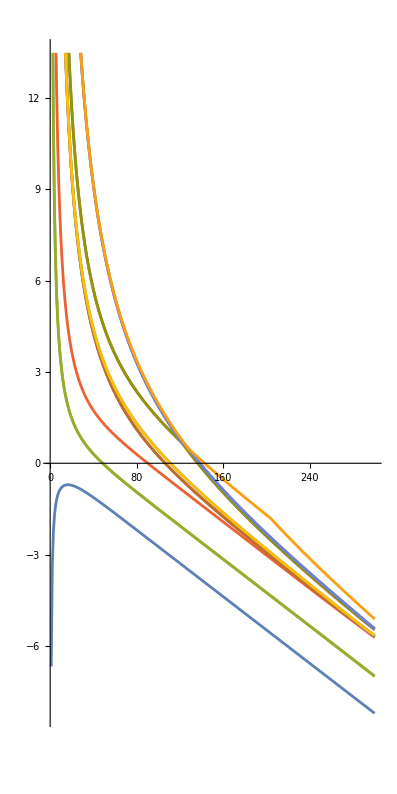

```mathematica
PlotL11=ListLinePlot[Transpose[EnergyTableL11],AspectRatio->2]
```

```mathematica
EnergyTableL11P=Table[(EnergyTableL11[[i]][[1;;10]]-EnergyTableL11[[i]][[1]])/(EnergyTableL11[[i]][[2]]-EnergyTableL11[[i]][[1]])//Chop,{i,1,300}];
```

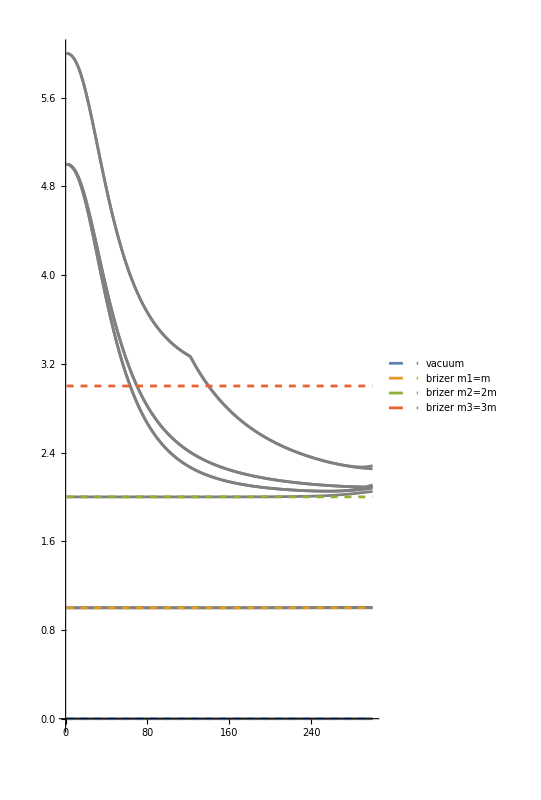

```mathematica
Show[ListLinePlot[Transpose[EnergyTableL11P],AspectRatio->2,PlotStyle->Gray],Plot[{0,1,2,3},{x,1,300},PlotStyle->Dashed,PlotLegends->{"vacuum","brizer m1=m","brizer m2=2m","brizer m3=3m"}]]
```

```mathematica
Length[Basis[11]]
```

365

```mathematica
HPI[13,x]
```

```mathematica
EnergyTableL13=Table[Sort[1/(i/100)Eigenvalues[H13[-(i/100)^(12/5)]]][[1;;7]]//Chop,{i,1,350}];
```

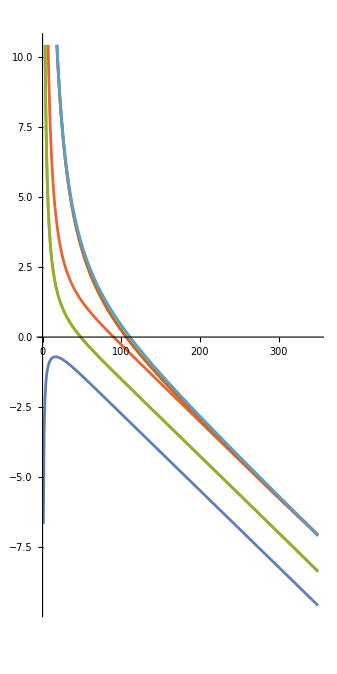

```mathematica
PlotL13=ListLinePlot[Transpose[EnergyTableL13],AspectRatio->2]
```

```mathematica
EnergyTableL13P=Table[(EnergyTableL13[[i]][[1;;7]]-EnergyTableL13[[i]][[1]])/(EnergyTableL13[[i]][[2]]-EnergyTableL13[[i]][[1]])//Chop,{i,1,350}];
```

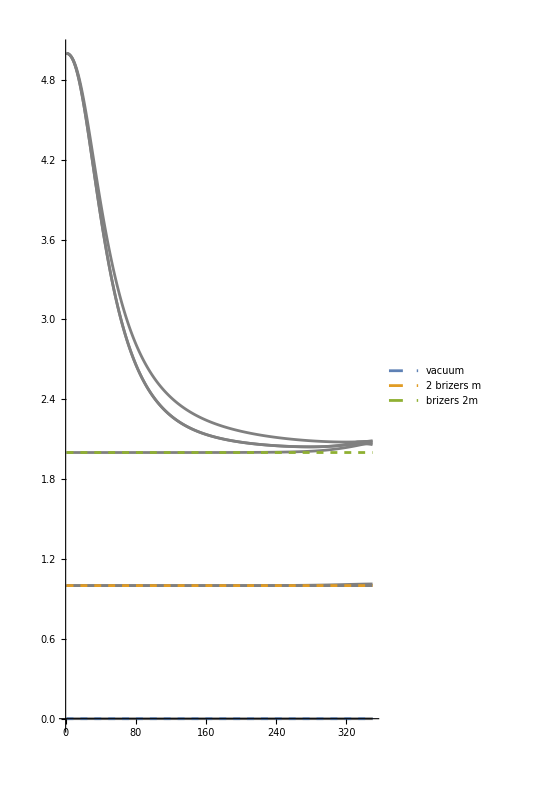

```mathematica
Show[ListLinePlot[Transpose[EnergyTableL13P],AspectRatio->2,PlotStyle->Gray],Plot[{0,1,2},{x,1,350},PlotStyle->Dashed,PlotLegends->{"vacuum","2 brizers m","brizers 2m"}]]
```